Sebastian Murk (sebastian.murk@oist.jp) [ORCID ID: 0000-0001-7296-0420]

Quantum Gravity Unit, Okinawa Institute of Science and Technology, 1919-1 Tancha, Onna-son, Okinawa 904-0495, Japan

Ioannis Soranidis (ioannis.soranidis@hdr.mq.edu.au) [ORCID ID: 0000-0002-8652-9874]

School of Mathematical and Physical Sciences, Macquarie University, Sydney, New South Wales 2109, Australia

# Light rings and causality for nonsingular ultracompact objects sourced by nonlinear electrodynamics [arXiv:2406.?????]

## [0] Preliminaries

Generic form of the NED Lagrangian density [Eqs. (3.4) and (3.3)]

```mathematica
ℒ[ℱ_,μ_,ν_,α_]:=(4μ(α ℱ)^((ν+3)/4))/(α(1+(α ℱ)^(ν/4))^(1+μ/ν));
```

```mathematica
ℱ[r_]:=(2 Subscript[Q, m]^2)/r^4;
```

Generic form of the metric function f(r) [Eq. (3.5)]

```mathematica
f[r_,μ_,ν_,α_,q_]:=1-(2 q^3 r^(μ-1))/(α(r^ν+q^ν)^(μ/ν));
```

Components of the background metric tensor [Eq. (2.7)]

```mathematica
Subscript[g, tt][r_,μ_,ν_,α_,q_]:=-f[r,μ,ν,α,q];
```

```mathematica
Subscript[g, rr][r_,μ_,ν_,α_,q_]:=f[r,μ,ν,α,q]^-1;
```

```mathematica
Subscript[g, θθ][r_]:=r^2;
```

```mathematica
Subscript[g, ϕϕ][r_,θ_]:=r^2 Sin[θ]^2;
```

Components of the effective metric tensor [Eqs. (3.6)-(3.8)]

```mathematica
Subscript[ℊ, 𝓉𝓉][r_,μ_,ν_,α_,q_]:=Subscript[g, tt][r,μ,ν,α,q];
```

```mathematica
Subscript[ℊ, 𝓇𝓇][r_,μ_,ν_,α_,q_]:=Subscript[g, rr][r,μ,ν,α,q];
```

```mathematica
Subscript[ℊ, θθ][ℱ_,r_,μ_,ν_,α_]:=Subscript[g, θθ][r](1+(2ℱ[r] D[D[ℒ[ℱ,μ,ν,α],ℱ],ℱ])/D[ℒ[ℱ,μ,ν,α],ℱ])^-1;
```

```mathematica
Subscript[ℊ, ϕϕ][ℱ_,r_,μ_,ν_,α_,θ_]:=Subscript[g, ϕϕ][r,θ](1+(2ℱ[r] D[D[ℒ[ℱ,μ,ν,α],ℱ],ℱ])/D[ℒ[ℱ,μ,ν,α],ℱ])^-1;
```

Potentials for the background and effective geometry [Eqs. (5.5) and (5.7)]. Note that in both cases g_tt g_rr=-f/f=-1 and thus V(r) = L^2/(g_rr g_ϕϕ)- E^2.

```mathematica
V[r_,μ_,ν_,α_,q_]:=Assuming[{μ>0,ν>0,α>0,q>0},L^2/(Subscript[g, rr][r,μ,ν,α,q]Subscript[g, ϕϕ][r,π/2])-En^2//FullSimplify];
```

```mathematica
𝒱[r_,μ_,ν_,α_,q_]:=Assuming[{μ>0,ν>0,α>0,q>0},L^2/(Subscript[ℊ, 𝓇𝓇][r,μ,ν,α,q]Subscript[ℊ, ϕϕ][ℱ,r,μ,ν,α,π/2])-En^2/.{ℱ->ℱ[r]}//FullSimplify];
```

Light ring locations from H function [Eq. (5.8)]

```mathematica
H[r_,μ_,ν_,α_,q_]:=(√(-Subscript[g, tt][r,μ,ν,α,q]Subscript[g, ϕϕ][r,π/2]))/(Subscript[g, ϕϕ][r,π/2]);
```

```mathematica
ℋ[r_,μ_,ν_,α_,q_]:=(√(-Subscript[ℊ, 𝓉𝓉][r,μ,ν,α,q]Subscript[ℊ, ϕϕ][ℱ,r,μ,ν,α,π/2]))/(Subscript[ℊ, ϕϕ][ℱ,r,μ,ν,α,π/2])/.{ℱ->ℱ[r]};
```

Define function to evaluate the causality condition

```mathematica
𝒞𝒶𝓊𝓈𝒶ℓ𝒾𝓉𝓎[ℱ_,μ_,ν_,α_]:=D[D[ℒ[ℱ,μ,ν,α],ℱ],ℱ]/D[ℒ[ℱ,μ,ν,α],ℱ];
```

## [I] Bardeen model [Sec. IV.1]

#### Metric function f_B(r) [Eq. (4.1)]

```mathematica
Subscript[f, B][r_]:=f[r,3,2,ℓ^3/M,ℓ]
```

```mathematica
Subscript[f, B][r]
```

1-(2 M r^2)/((r^2+ℓ^2)^(3/2))

#### NED Lagrangian density [Eq. (4.4)]

```mathematica
ℒ[ℱ,3,2,α]
```

(12 (ℱ α)^(5/4))/(α (1+√(ℱ α))^(5/2))

```mathematica
Assuming[{α>0},ℒ[ℱ,3,2,α]//Simplify]
```

(12 ℱ (ℱ α)^(1/4))/(1+√(ℱ α))^(5/2)

## [I.1] Horizon locations, critical length, and effective metric

```mathematica
Solve[Subscript[f, B][r]==0,r]//Simplify;
```

```mathematica
SubPlus[rB][M_,ℓ_]=Solve[Subscript[f, B][r]==0,r][[2,1,2]];
```

```mathematica
SubMinus[rB][M_,ℓ_]=Solve[Subscript[f, B][r]==0,r][[4,1,2]];
```

#### Series expansions of horizons about ℓ = 0 [Eqs. (4.5) and (4.6)]

```mathematica
Assuming[{M>0,ℓ>0},Series[SubPlus[rB][M,ℓ],{ℓ,0,4}]//Simplify]
```

2 M-(3 ℓ^2)/(4 M)-(21 ℓ^4)/(64 M^3)+O[ℓ]^5

```mathematica
Assuming[{M>0,ℓ>0},Series[SubMinus[rB][M,ℓ],{ℓ,0,4}]//Simplify]
```

ℓ^(3/2)/(√2 √M)+(3 ℓ^(5/2))/(8 √2 M^(3/2))+(33 ℓ^(7/2))/(128 √2 M^(5/2))+O[ℓ]^(9/2)

#### Critical length [Eq. (4.7)]

```mathematica
Solve[D[Subscript[f, B][r],r]==0/.{r->SubPlus[rB][M,ℓ]} ,ℓ]
```

{{ℓ→0},{ℓ→-√(2/3) M},{ℓ→√(2/3) M},{ℓ→-(4 M)/(3 √3)},{ℓ→(4 M)/(3 √3)}}

```mathematica
Solve[SubPlus[rB][M,ℓ]==SubMinus[rB][M,ℓ],ℓ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ℓ→0},{ℓ→-√(2/3) M},{ℓ→√(2/3) M},{ℓ→-(4 M)/(3 √3)},{ℓ→(4 M)/(3 √3)}}

```mathematica
Subscript[ℬℓ, c]=4/(3 √3);
```

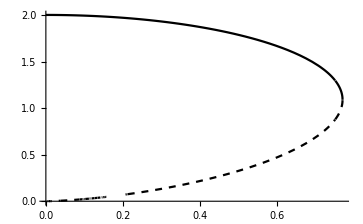

```mathematica
Plot[{SubPlus[rB][1,ℓ],SubMinus[rB][1,ℓ]},{ℓ,0,Subscript[ℬℓ, c]},PlotStyle->{Black,{Black,Dashed}}]
```

#### Effective metric tensor components [Eqs. (4.9) and (4.10)]

```mathematica
Assuming[{ℓ>0,r>0},(1+(2ℱ[r] D[D[ℒ[ℱ,3,2,ℓ^3/M],ℱ],ℱ])/D[ℒ[ℱ,3,2,ℓ^3/M],ℱ])/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->√((M ℓ)/2)}//FullSimplify]
```

-2+(7 r^2)/(2 (r^2+ℓ^2))

```mathematica
-2+(7 r^2)/(2 (r^2+ℓ^2))-(3/2-(7 ℓ^2)/(2 (ℓ^2+r^2)))//Simplify
```

0

## [I.2] Light rings

### [I.2.1] Light rings in the background geometry

#### [I.2.1.1] Light rings in the background geometry: Locations and critical length

Potential in the background geometry [Eq. (5.9)]

```mathematica
V[r,3,2,ℓ^3/M,ℓ]
```

-En^2+L^2 (1/r^2-(2 M)/((r^2+ℓ^2)^(3/2)))

```mathematica
Assuming[{ℓ>0,M>0,r>0},V[r,3,2,ℓ^3/M,ℓ]//FullSimplify]
```

-En^2+L^2 (1/r^2-(2 M)/((r^2+ℓ^2)^(3/2)))

```mathematica
D[V[r,3,2,ℓ^3/M,ℓ],r]
```

L^2 (-2/r^3+(6 M r)/((r^2+ℓ^2)^(5/2)))

```mathematica
D[D[V[r,3,2,ℓ^3/M,ℓ],r],r]//Simplify
```

6 L^2 (1/r^4-(5 M r^2)/((r^2+ℓ^2)^(7/2))+M/((r^2+ℓ^2)^(5/2)))

Determination of light ring locations

```mathematica
Solve[D[V[r,3,2,ℓ^3/M,ℓ],r]==0,r]
```

{{r→-√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,1]},{r→√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,1]},{r→-√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,2]},{r→√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,2]},{r→-√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,3]},{r→√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,3]},{r→-√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,4]},{r→√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,4]},{r→-√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,5]},{r→√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,5]}}

Alternative method using Eq. (5.8)

```mathematica
D[H[r,3,2,ℓ^3/M,ℓ],r]//Simplify
```

(3 M r^4-(r^2+ℓ^2)^(5/2))/(r (r^2+ℓ^2)^(5/2) √(r^2-(2 M r^4)/((r^2+ℓ^2)^(3/2))))

```mathematica
Solve[D[H[r,3,2,ℓ^3/M,ℓ],r]==0,r]
```

{{r→-√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,1]},{r→√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,1]},{r→-√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,2]},{r→√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,2]},{r→-√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,3]},{r→√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,3]},{r→-√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,4]},{r→√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,4]},{r→-√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,5]},{r→√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,5]}}

Identification of inner and outer light ring in the background geometry

```mathematica
BoutLRbkg[M_,ℓ_]:=√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,3]
```

```mathematica
BinLRbkg[M_,ℓ_]:=√Root[ℓ^10+5 ℓ^8 #1+10 ℓ^6 #1^2+10 ℓ^4 #1^3+(-9 M^2+5 ℓ^2) #1^4+#1^5&,2]
```

Determination of critical light ring length for the background geometry

```mathematica
FindRoot[BoutLRbkg[1,ℓ]==BinLRbkg[1,ℓ],{ℓ,0.8}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{ℓ→0.85865}

```mathematica
Subscript[ℬLRbkgℓ, c]=0.8586501033589531;
```

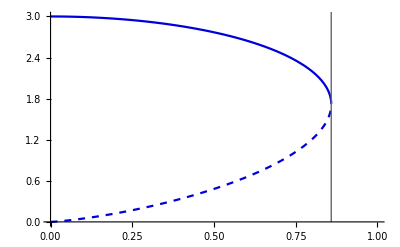

```mathematica
Plot[{BoutLRbkg[1,ℓ],BinLRbkg[1,ℓ]},{ℓ,0,1},PlotStyle->{Darker[Blue,0.15],{Darker[Blue,0.15],Dashed}},Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℬLRbkgℓ, c],0},{Subscript[ℬLRbkgℓ, c],3.1}}]}]
```

#### [I.2.1.2] Light rings in the background geometry: Dynamical behavior

```mathematica
D[D[V[r,3,2,ℓ^3/M,ℓ],r],r]
```

L^2 (6/r^4-(30 M r^2)/((r^2+ℓ^2)^(7/2))+(6 M)/((r^2+ℓ^2)^(5/2)))

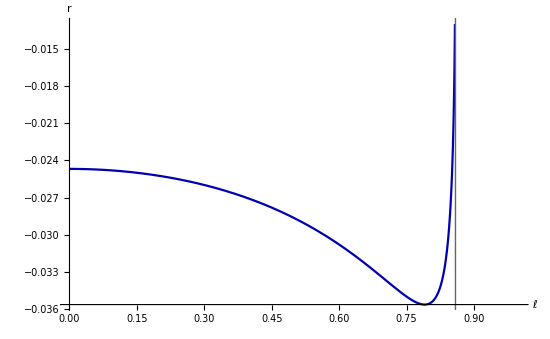

```mathematica
Plot[D[D[V[r,3,2,ℓ^3/M,ℓ],r],r]/.{M->1,L->1}/.{r->BoutLRbkg[1,ℓ]},{ℓ,0,1},PlotRange->{{0,1},Automatic},PlotStyle->{Darker[Blue,0.3]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℬLRbkgℓ, c],0},{Subscript[ℬLRbkgℓ, c],-1}}]}]
```

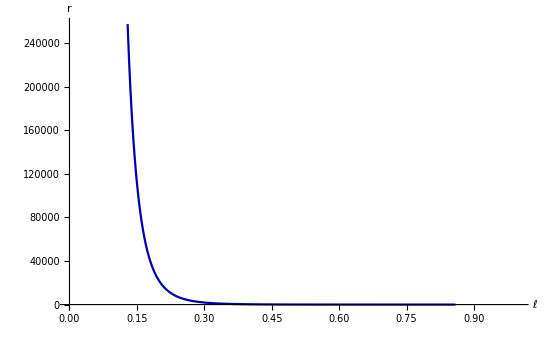

```mathematica
Plot[D[D[V[r,3,2,ℓ^3/M,ℓ],r],r]/.{M->1,L->1}/.{r->BinLRbkg[1,ℓ]},{ℓ,0,1},PlotRange->{{0,1},Automatic},PlotStyle->{Darker[Blue,0.3]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℬLRbkgℓ, c],0},{Subscript[ℬLRbkgℓ, c],-1}}]}]
```

### [I.2.2] Light rings in the effective geometry

#### [I.2.2.1] Light rings in the effective geometry: Locations and critical length

```mathematica
Subscript[𝒱, B][r_,M_,ℓ_]:=𝒱[r,3,2,ℓ^3/M,ℓ]/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify
```

Potential in the effective geometry [Eq. (5.12)]

```mathematica
Assuming[{ℓ>0,M>0,r>0},Subscript[𝒱, B][r,M,ℓ]//FullSimplify]
```

-En^2+(L^2 (3 r^2-4 ℓ^2) (-2 M r^2+(r^2+ℓ^2)^(3/2)))/(2 r^2 (r^2+ℓ^2)^(5/2))

```mathematica
Subscript[d𝒱, B][r_,M_,ℓ_]=Assuming[{ℓ>0,M>0,r>0},D[Subscript[𝒱, B][r,M,ℓ],r]//Simplify];
```

```mathematica
Solve[Subscript[d𝒱, B][r,M,ℓ]==0,r]
```

{{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,1]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,1]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,2]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,2]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,3]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,3]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,4]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,4]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,5]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,5]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,6]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,6]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,7]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 M^2 ℓ^4+49 ℓ^6) #1^4+(468 M^2 ℓ^2-77 ℓ^4) #1^5+(-81 M^2-21 ℓ^2) #1^6+9 #1^7&,7]}}

```mathematica
Solve[Subscript[d𝒱, B][r,M,ℓ]==0,r]/.{M->1}//Simplify
```

{{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,1]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,1]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,2]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,2]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,3]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,3]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,4]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,4]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,5]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,5]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,6]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,6]},{r→-√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,7]},{r→√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,7]}}

Identification of inner and outer light ring in the effective geometry

General::munfl: 0.0000245143^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000245143^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000245143^72 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

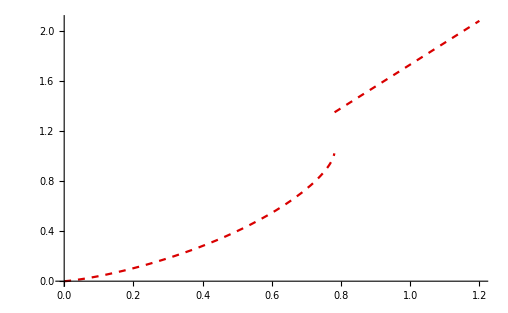

```mathematica
Plot[√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,2],{ℓ,0,1.2},PlotStyle->{{Darker[Red,0.15],Dashed}}]
```

```mathematica
Root2[ℓ_]:=√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,2];
```

```mathematica
BinLReffbottom[ℓ_]:=If[Root2[ℓ]<1.2,Root2[ℓ],Nothing];
```

General::munfl: 0.0000245143^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000245143^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000245143^72 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

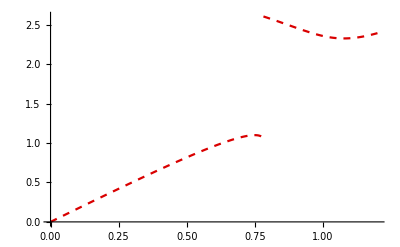

```mathematica
Plot[√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,3],{ℓ,0,1.2},PlotStyle->{{Darker[Red,0.15],Dashed}}]
```

```mathematica
Root3[ℓ_]:=√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,3];
```

```mathematica
BinLRefftop[ℓ_]:=If[Root3[ℓ]<1.5,Root3[ℓ],Nothing];
```

```mathematica
BoutLReffbottom[ℓ_]:=If[Root3[ℓ]>1.5,Root3[ℓ],Nothing];
```

General::munfl: 0.0000245143^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000245143^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000245143^72 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

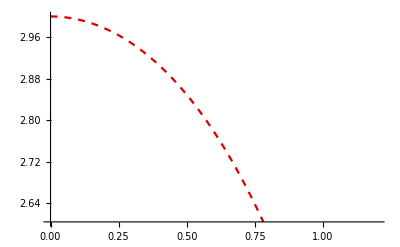

```mathematica
Plot[√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,5],{ℓ,0,1.2},PlotStyle->{{Darker[Red,0.15],Dashed}}]
```

```mathematica
BoutLRefftop[ℓ_]:=√Root[16 ℓ^14+112 ℓ^12 #1+280 ℓ^10 #1^2+280 ℓ^8 #1^3+(-676 ℓ^4+49 ℓ^6) #1^4+(468 ℓ^2-77 ℓ^4) #1^5+(-81-21 ℓ^2) #1^6+9 #1^7&,5];
```

General::munfl: 0.0000286^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000286^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000286^72 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

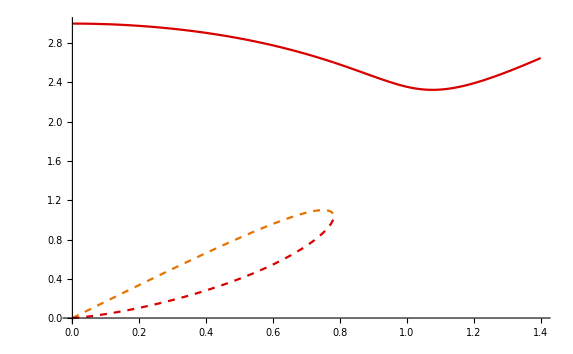

```mathematica
Plot[{BoutLRefftop[ℓ],BoutLReffbottom[ℓ],BinLRefftop[ℓ],BinLReffbottom[ℓ]},{ℓ,0,1.4},PlotStyle->{Darker[Red,0.15],Darker[Red,0.15],{Darker[Orange,0.10],Dashed},{Darker[Red,0.15],Dashed}}]
```

Determination of critical light ring length for the effective geometry

```mathematica
FindRoot[Root3[ℓ]==Root2[ℓ],{ℓ,0.7}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{ℓ→0.781099}

```mathematica
Subscript[ℬLReffℓ, c]=0.7810990615755589;
```

```mathematica
FindMinimum[BoutLReffbottom[ℓ],{ℓ,0.9}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.32506,{ℓ→1.07663}}

```mathematica
FindMinimum[BoutLReffbottom[ℓ],{ℓ,1.0}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.32506,{ℓ→1.07663}}

```mathematica
FindMinimum[BoutLReffbottom[ℓ],{ℓ,1.1}]
```

{2.32506,{ℓ→1.07663}}

#### [I.2.2.2] Light rings in the effective geometry: Dynamical behavior

```mathematica
Subscript[dd𝒱, B][r_,M_,ℓ_]=Assuming[{ℓ>0,M>0,r>0},D[Subscript[d𝒱, B][r,M,ℓ],r]//Simplify];
```

```mathematica
D[D[V[r,3,2,ℓ^3/M,ℓ],r],r]
```

L^2 (6/r^4-(30 M r^2)/((r^2+ℓ^2)^(7/2))+(6 M)/((r^2+ℓ^2)^(5/2)))

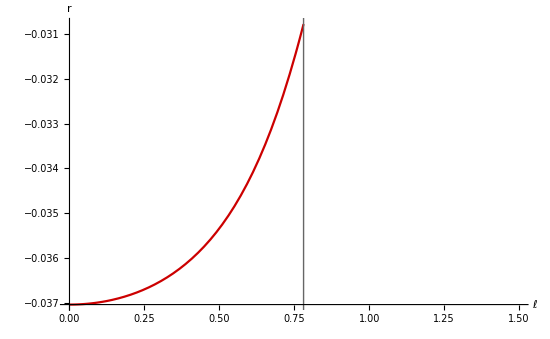

```mathematica
Plot[Subscript[dd𝒱, B][r,M,ℓ]/.{M->1,L->1}/.{r->BoutLRefftop[ℓ]},{ℓ,0,1},PlotRange->{{0,1.5},Automatic},PlotStyle->{Darker[Red,0.2]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->45,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℬLReffℓ, c],0},{Subscript[ℬLReffℓ, c],-1}}]}]
```

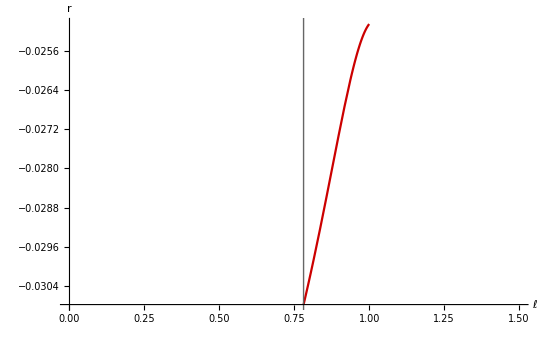

```mathematica
Plot[Subscript[dd𝒱, B][r,M,ℓ]/.{M->1,L->1}/.{r->BoutLReffbottom[ℓ]},{ℓ,0,1},PlotRange->{{0,1.5},Automatic},PlotStyle->{Darker[Red,0.2]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->45,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℬLReffℓ, c],0},{Subscript[ℬLReffℓ, c],-1}}]}]
```

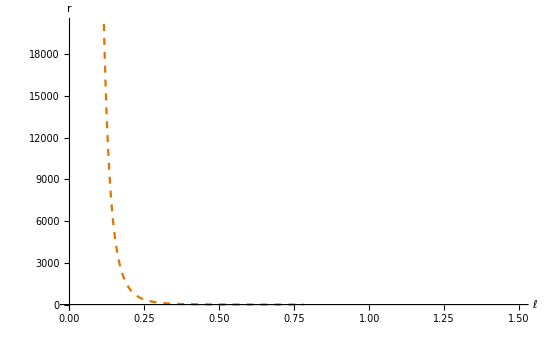

```mathematica
Plot[Subscript[dd𝒱, B][r,M,ℓ]/.{M->1,L->1}/.{r->BinLRefftop[ℓ]},{ℓ,0,1},PlotRange->{{0,1.5},Automatic},PlotStyle->{Darker[Orange,0.1],Dashed},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->55,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℬLReffℓ, c],0},{Subscript[ℬLReffℓ, c],1}}]}]
```

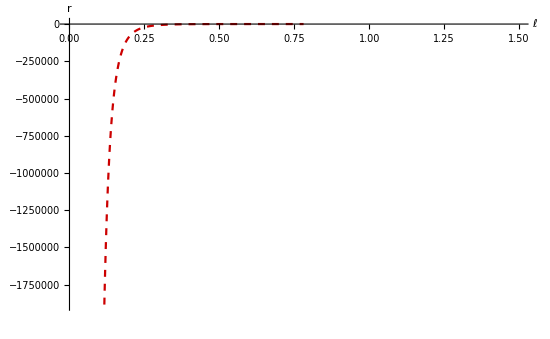

```mathematica
Plot[Subscript[dd𝒱, B][r,M,ℓ]/.{M->1,L->1}/.{r->BinLReffbottom[ℓ]},{ℓ,0,1},PlotRange->{{0,1.5},Automatic},PlotStyle->{Darker[Red,0.2],Dashed},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->55,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℬLReffℓ, c],0},{Subscript[ℬLReffℓ, c],-1}}]}]
```

### [I.2.3] Figure 1a: Horizons and light rings

General::munfl: (1.95068×10^-6)^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.95068×10^-6)^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.95068×10^-6)^72 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

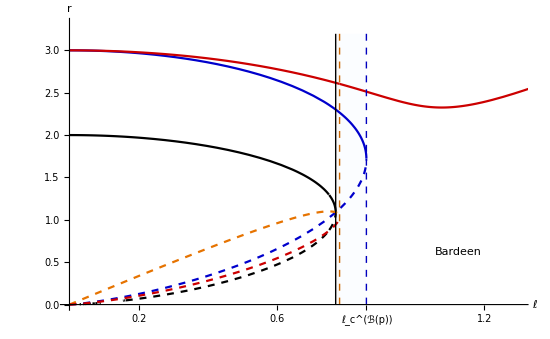

```mathematica
Plot[{SubPlus[rB][1,ℓ],SubMinus[rB][1,ℓ],BoutLRbkg[1,ℓ],BinLRbkg[1,ℓ],BoutLRefftop[ℓ],BoutLReffbottom[ℓ],BinLRefftop[ℓ],BinLReffbottom[ℓ]},{ℓ,0,1.5},PlotStyle->{Black,{Black,Dashed},Darker[Blue,0.2],{Darker[Blue,0.2],Dashed},Darker[Red,0.2],Darker[Red,0.2],{Darker[Orange,0.10],Dashed},{Darker[Red,0.2],Dashed}},PlotRange->{{0,1.3},{0,3.31}},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],Ticks->{{0.2,0.4,0.6,{Subscript[ℬℓ, c],"ℓ_c^ℬ"},{Subscript[ℬLRbkgℓ, c],"ℓ_c^(<ℬ(p)>)"},{1.0,"1.0"},{1.2,"1.2"},{1.4,"1.4"},{1.6,"1.6"},{1.8,"1.8"}},Automatic},TicksStyle->Directive[FontSize->13],ImageSize->550,Prolog->{Opacity[0.10,LightBlue],Rectangle[{Subscript[ℬℓ, c],0},{Subscript[ℬLRbkgℓ, c],3.195}],Opacity[0.15,LightOrange],Rectangle[{Subscript[ℬℓ, c],0},{Subscript[ℬLReffℓ, c],3.195}]},Epilog->{Inset[Framed["Bardeen",RoundingRadius->2],Scaled[{0.85,0.20}]],{Directive[Thickness->0.0013,Darker[Black,0.2]],Line[{{Subscript[ℬℓ, c],0},{Subscript[ℬℓ, c],3.195}}]},{Directive[Thickness->0.0011,Darker[Orange,0.2],Dashed],Line[{{Subscript[ℬLReffℓ, c],0},{Subscript[ℬLReffℓ, c],3.195}}]},{Directive[Thickness->0.0013,Darker[Blue,0.25],Dashed],Line[{{Subscript[ℬLRbkgℓ, c],0},{Subscript[ℬLRbkgℓ, c],3.195}}]}}]
```

### [I.2.4] Figure 2a: Difference between the outer LR in the effective vs. outer LR in the background geometry

```mathematica
BLRdiff1[ℓ_]:=BoutLRefftop[ℓ]-BoutLRbkg[1,ℓ];
```

```mathematica
BLRdiff2[ℓ_]:=BoutLReffbottom[ℓ]-BoutLRbkg[1,ℓ];
```

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^72 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

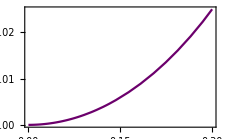

```mathematica
ℬdiffSmallℓ=Plot[{BLRdiff1[ℓ]},{ℓ,0,1},PlotStyle->{Darker[Purple,0.15],Darker[Purple,0.15]},PlotRange->{{0,0.30},{0,0.025}},Frame->True,ImageSize->225]
```

Scaling behavior in the limit ℓ->0

```mathematica
Limit[D[BLRdiff1[ℓ],ℓ],ℓ->0]
```

0

```mathematica
Limit[D[D[BLRdiff1[ℓ],ℓ],ℓ],ℓ->0]/2
```

7/27

```mathematica
Limit[D[D[D[BLRdiff1[ℓ],ℓ],ℓ],ℓ],ℓ->0]/6
```

0

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^72 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

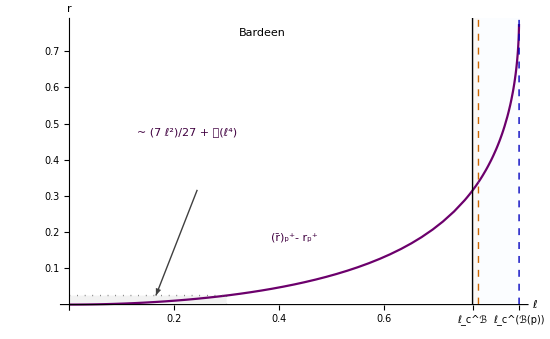

```mathematica
Plot[{BLRdiff1[ℓ],BLRdiff2[ℓ]},{ℓ,0,1},PlotStyle->{Darker[Purple,0.15],Darker[Purple,0.15]},PlotRange->{{0,1.05},{All,0.775}},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],Ticks->{{0.2,0.4,0.6,{Subscript[ℬℓ, c],"ℓ_c^ℬ"},{Subscript[ℬLRbkgℓ, c],"ℓ_c^(<ℬ(p)>)"},{1.0,"1.0"}},{0.1,0.2,0.3,0.4,0.5,0.6,0.7}},TicksStyle->Directive[FontSize->13],ImageSize->550,Prolog->{Opacity[0.10,Gray],Rectangle[{0,0},{0.30,0.025}],Opacity[0.10,LightBlue],Rectangle[{Subscript[ℬℓ, c],0},{Subscript[ℬLRbkgℓ, c],3.115}],Opacity[0.15,LightOrange],Rectangle[{Subscript[ℬℓ, c],0},{Subscript[ℬLReffℓ, c],3.115}]},Epilog->{Inset[ℬdiffSmallℓ,Scaled[{0.30,0.60}]],Inset[Framed["Bardeen",RoundingRadius->2],Scaled[{0.432,0.95}]],Inset[Style["(r̄)_p^(<+>)- r_p^(<+>)",Darker[Purple,0.50]],Scaled[{0.50,0.25}]],Inset[Style["~ (7 ℓ^2)/27 + 𝒪(ℓ^4)",Darker[Purple,0.50]],Scaled[{0.27,0.61}]],{Directive[Thickness->0.0013,Darker[Gray,0.5]],Arrowheads[0.03],Arrow[{{0.244,0.317},{0.165,0.025}}]},
{Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{0,0.025},{0.30,0.025}}]},{Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{0.30,0},{0.30,0.025}}]},{Directive[Thickness->0.0013,Darker[Black,0.2]],Line[{{Subscript[ℬℓ, c],0},{Subscript[ℬℓ, c],1}}]},{Directive[Thickness->0.0011,Darker[Orange,0.2],Dashed],Line[{{Subscript[ℬLReffℓ, c],0},{Subscript[ℬLReffℓ, c],1}}]},{Directive[Thickness->0.0015,Darker[Blue,0.25],Dashed],Line[{{Subscript[ℬLRbkgℓ, c],0},{Subscript[ℬLRbkgℓ, c],1}}]}}]
```

## [I.3] Phase velocities

#### First- and second-order derivatives of NED Lagrangian density [Eqs. (6.13) and (6.14)]

```mathematica
Assuming[{r>0,M>0,ℓ>0},D[ℒ[ℱ,3,2,ℓ^3/M],ℱ]/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify]
```

(15 r^6 ℓ)/((r^2+ℓ^2)^(7/2))

```mathematica
Assuming[{r>0,M>0,ℓ>0},D[D[ℒ[ℱ,3,2,ℓ^3/M],ℱ],ℱ]/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify]
```

(15 r^10 (r^2-6 ℓ^2))/(4 M (r^2+ℓ^2)^(9/2))

#### Phase velocities in the background and effective geometry [Eqs. (6.15) and (6.16)]

```mathematica
√(Subscript[f, B][r])
```

√(1-(2 M r^2)/((r^2+ℓ^2)^(3/2)))

```mathematica
ℬ𝒷𝓀ℊvph[r_,M_,ℓ_]:=√(1-(2 M r^2)/((r^2+ℓ^2)^(3/2)));
```

```mathematica
Assuming[{r>0,M>0,ℓ>0},√(Subscript[f, B][r](1+(2ℱ[r] D[D[ℒ[ℱ,3,2,ℓ^3/M],ℱ],ℱ])/D[ℒ[ℱ,3,2,ℓ^3/M],ℱ] Sin[η]^2))/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify]
```

1/2 √(-((r^4+ℓ^4+2 r^2 (ℓ^2-M √(r^2+ℓ^2))) (-5 r^2+2 ℓ^2+(r^2-6 ℓ^2) Cos[2 η]))/((r^2+ℓ^2)^3))

```mathematica
ℬℯ𝒻𝒻vph[r_,M_,ℓ_,η_]:=1/2 √(-((r^4+ℓ^4+2 r^2 (ℓ^2-M √(r^2+ℓ^2))) (-5 r^2+2 ℓ^2+(r^2-6 ℓ^2) Cos[2 η]))/((r^2+ℓ^2)^3));
```

```mathematica
Assuming[{r>0,M>0,ℓ>0},(1+(2ℱ[r] D[D[ℒ[ℱ,3,2,ℓ^3/M],ℱ],ℱ])/D[ℒ[ℱ,3,2,ℓ^3/M],ℱ] Sin[η]^2)/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify]
```

1+((r^2-6 ℓ^2) Sin[η]^2)/(2 (r^2+ℓ^2))

## [II] Hayward model [Sec. IV.2]

#### Metric function f_H(r) [Eq. (4.11)]

```mathematica
Subscript[f, H][r_]:=f[r,3,3,2 ℓ^2,(2M ℓ^2)^(1/3)]
```

```mathematica
Subscript[f, H][r]
```

1-(2 M r^2)/(r^3+2 M ℓ^2)

#### NED Lagrangian density [Eq. (4.14)]

```mathematica
ℒ[ℱ,3,3,α]
```

(12 (ℱ α)^(3/2))/(α (1+(ℱ α)^(3/4))^2)

```mathematica
Assuming[{α>0},ℒ[ℱ,3,3,α]//Simplify]
```

(12 ℱ √(ℱ α))/((1+(ℱ α)^(3/4))^2)

## [II.1] Horizon locations and critical length

```mathematica
Solve[Subscript[f, H][r]==0,r]//Simplify
```

{{r→1/3 (2 M+(4 M^2)/((8 M^3-27 M ℓ^2+3 √(-48 M^4 ℓ^2+81 M^2 ℓ^4))^(1/3))+(8 M^3-27 M ℓ^2+3 √(-48 M^4 ℓ^2+81 M^2 ℓ^4))^(1/3))},{r→(2 M)/3-(2 ⅈ (-ⅈ+√3) M^2)/(3 (8 M^3-27 M ℓ^2+3 √(-48 M^4 ℓ^2+81 M^2 ℓ^4))^(1/3))+1/6 ⅈ (ⅈ+√3) (8 M^3-27 M ℓ^2+3 √(-48 M^4 ℓ^2+81 M^2 ℓ^4))^(1/3)},{r→(2 M)/3+(2 ⅈ (ⅈ+√3) M^2)/(3 (8 M^3-27 M ℓ^2+3 √(-48 M^4 ℓ^2+81 M^2 ℓ^4))^(1/3))-1/6 ⅈ (-ⅈ+√3) (8 M^3-27 M ℓ^2+3 √(-48 M^4 ℓ^2+81 M^2 ℓ^4))^(1/3)}}

```mathematica
SubPlus[rH][M_,ℓ_]=Solve[Subscript[f, H][r]==0,r][[1,1,2]];
```

```mathematica
SubMinus[rH][M_,ℓ_]=Solve[Subscript[f, H][r]==0,r][[3,1,2]];
```

#### Series expansions of horizons about ℓ = 0 [Eqs. (4.15) and (4.16)]

```mathematica
Assuming[{M>0,ℓ>0},Series[SubPlus[rH][M,ℓ],{ℓ,0,4}]//Simplify]
```

2 M-ℓ^2/(2 M)-ℓ^4/(4 M^3)+O[ℓ]^5

```mathematica
Assuming[{M>0,ℓ>0},Series[SubMinus[rH][M,ℓ],{ℓ,0,4}]//Simplify]
```

ℓ+ℓ^2/(4 M)+(5 ℓ^3)/(32 M^2)+ℓ^4/(8 M^3)+O[ℓ]^5

#### Critical length [Eq. (4.17)]

```mathematica
Solve[D[Subscript[f, H][r],r]==0/.{r->SubPlus[rH][M,ℓ]} ,ℓ]
```

{{ℓ→-(4 M)/(3 √3)},{ℓ→(4 M)/(3 √3)}}

```mathematica
Solve[SubPlus[rH][M,ℓ]==SubMinus[rH][M,ℓ],ℓ]
```

{{ℓ→0},{ℓ→-(4 M)/(3 √3)},{ℓ→(4 M)/(3 √3)}}

```mathematica
Subscript[ℋℓ, c]=4/(3 √3);
```

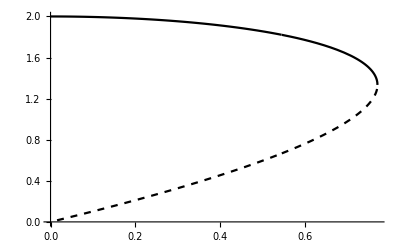

```mathematica
Plot[{SubPlus[rH][1,ℓ],SubMinus[rH][1,ℓ]},{ℓ,0,4/(3 √3)},PlotStyle->{Black,{Black,Dashed}}]
```

#### Effective metric tensor components [Eqs. (4.19) and (4.20)]

```mathematica
Assuming[{α>0,r>0,M>0,ℓ>0},1+(2ℱ[r] D[D[ℒ[ℱ,3,3,2 ℓ^2],ℱ],ℱ])/D[ℒ[ℱ,3,3,2 ℓ^2],ℱ]/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->(M^(2/3)ℓ^(1/3))/2^(1/3)}//Simplify]
```

(2 r^3-5 M ℓ^2)/(r^3+2 M ℓ^2)

```mathematica
%-(2-(9 ℓ^2 M)/(2 ℓ^2 M+r^3))//Simplify
```

0

## [II.2] Light rings

### [II.2.1] Light rings in the background geometry

#### [II.2.1.1] Light rings in the background geometry: Locations and critical length

Potential in the background geometry [Eq. (5.10)]

```mathematica
V[r,3,3,2 ℓ^2,(2M ℓ^2)^(1/3)]
```

-En^2+L^2 (1/r^2-(2 M)/(r^3+2 M ℓ^2))

```mathematica
Solve[D[V[r,3,3,2 ℓ^2,(2M ℓ^2)^(1/3)],r]==0,r]//Simplify
```

{{r→Root[4 M^2 ℓ^4+4 M ℓ^2 #1^3-3 M #1^5+#1^6&,1]},{r→Root[4 M^2 ℓ^4+4 M ℓ^2 #1^3-3 M #1^5+#1^6&,2]},{r→Root[4 M^2 ℓ^4+4 M ℓ^2 #1^3-3 M #1^5+#1^6&,3]},{r→Root[4 M^2 ℓ^4+4 M ℓ^2 #1^3-3 M #1^5+#1^6&,4]},{r→Root[4 M^2 ℓ^4+4 M ℓ^2 #1^3-3 M #1^5+#1^6&,5]},{r→Root[4 M^2 ℓ^4+4 M ℓ^2 #1^3-3 M #1^5+#1^6&,6]}}

Identification of the physically relevant roots that represent the inner and outer light ring in the Hayward RBH model’s background geometry.
The second [first] root corresponds to the outer [inner] light ring.

```mathematica
HoutLRbkg[M_,ℓ_]:=Root[4 M^2 ℓ^4+4 M ℓ^2 #1^3-3 M #1^5+#1^6&,2];
```

```mathematica
HinLRbkg[M_,ℓ_]:=Root[4 M^2 ℓ^4+4 M ℓ^2 #1^3-3 M #1^5+#1^6&,1];
```

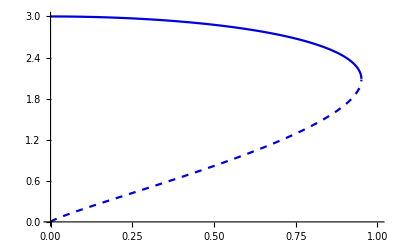

```mathematica
Plot[{HoutLRbkg[1,ℓ],HinLRbkg[1,ℓ]},{ℓ,0,1},PlotStyle->{Darker[Blue,0.15],{Darker[Blue,0.15],Dashed}}]
```

```mathematica
FindRoot[HoutLRbkg[1,ℓ]==HinLRbkg[1,ℓ],{ℓ,0.9}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{ℓ→0.950907}

```mathematica
Subscript[ℋbkgℓ𝓅, c]=0.950907217889236;
```

#### [II.2.1.2] Light rings in the background geometry: Dynamical behavior

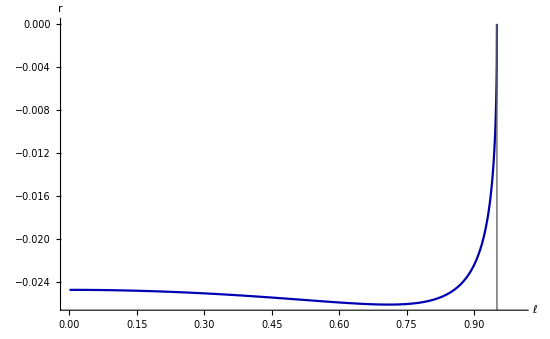

```mathematica
Plot[D[D[V[r,3,3,2 ℓ^2,(2M ℓ^2)^(1/3)],r],r]/.{M->1,L->1}/.{r->HoutLRbkg[1,ℓ]},{ℓ,0,Subscript[ℋbkgℓ𝓅, c]},PlotRange->{{0,1},All},PlotStyle->{Darker[Blue,0.3]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImagePadding->47,ImageSize->550,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℋbkgℓ𝓅, c],0},{Subscript[ℋbkgℓ𝓅, c],-1}}]}]
```

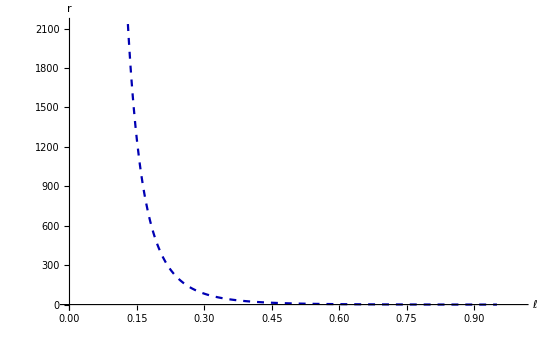

```mathematica
Plot[D[D[V[r,3,3,2 ℓ^2,(2M ℓ^2)^(1/3)],r],r]/.{M->1,L->1}/.{r->HinLRbkg[1,ℓ]},{ℓ,0,Subscript[ℋbkgℓ𝓅, c]},PlotRange->{{0,1},Automatic},PlotStyle->{Darker[Blue,0.3],Dashed},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImagePadding->47,ImageSize->550,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℋbkgℓ𝓅, c],0},{Subscript[ℋbkgℓ𝓅, c],1}}]}]
```

### [II.2.2] Light rings in the effective geometry

#### [II.2.2.1] Light rings in the effective geometry: Locations and critical length

```mathematica
Subscript[𝒱, H][r_,M_,ℓ_]:=𝒱[r,3,3,2 ℓ^2,(2M ℓ^2)^(1/3)]/.{Subscript[Q, m]->(M^(2/3)ℓ^(1/3))/2^(1/3)}//Simplify
```

Potential in the effective geometry [Eq. (5.13)]

```mathematica
Assuming[{ℓ>0,M>0,r>0},Subscript[𝒱, H][r,M,ℓ]//FullSimplify]
```

-En^2+(L^2 (2 r^3-5 M ℓ^2) (r^3+2 M (-r^2+ℓ^2)))/((r^4+2 M r ℓ^2)^2)

```mathematica
Subscript[d𝒱, H][r_,M_,ℓ_]=Assuming[{ℓ>0,M>0,r>0},D[Subscript[𝒱, H][r,M,ℓ],r]//Simplify];
```

```mathematica
Solve[Subscript[d𝒱, H][r,M,ℓ]==0,r]/.{M->1}//Simplify
```

{{r→Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,1]},{r→Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,2]},{r→Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,3]},{r→Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,4]},{r→Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,5]},{r→Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,6]},{r→Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,7]},{r→Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,8]},{r→Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,9]}}

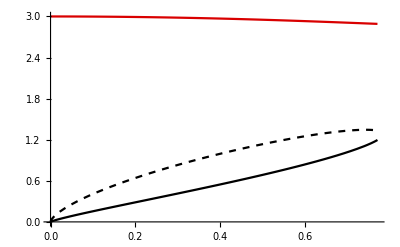

```mathematica
Plot[{Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,1],Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,2],Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,3],Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,4]},{ℓ,0,4/(3 √3)},PlotStyle->{Black,{Black,Dashed},Darker[Red,0.15],{Darker[Red,0.15],Dashed}}]
```

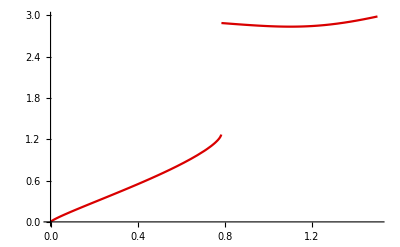

```mathematica
Plot[Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,1],{ℓ,0,1.5},PlotStyle->{Darker[Red,0.15]}]
```

```mathematica
Hroot1[ℓ_]:=Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,1];
```

```mathematica
HinLReffbottom[ℓ_]:=If[Hroot1[ℓ]<1.5,Hroot1[ℓ],Nothing];
```

```mathematica
HoutLReffbottom[ℓ_]:=If[Hroot1[ℓ]>1.5,Hroot1[ℓ],Nothing];
```

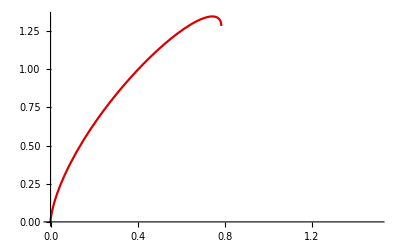

```mathematica
Plot[Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,2],{ℓ,0,1.5},PlotStyle->{Darker[Red,0.15]}]
```

```mathematica
HinLRefftop[ℓ_]:=Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,2];
```

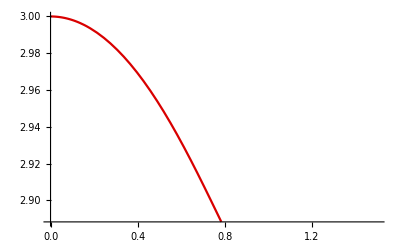

```mathematica
Plot[Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,3],{ℓ,0,1.5},PlotStyle->{Darker[Red,0.15]}]
```

```mathematica
HoutLRefftop[ℓ_]:=Root[-40 ℓ^6-78 ℓ^4 #1^3+84 ℓ^2 #1^5-21 ℓ^2 #1^6-12 #1^8+4 #1^9&,3];
```

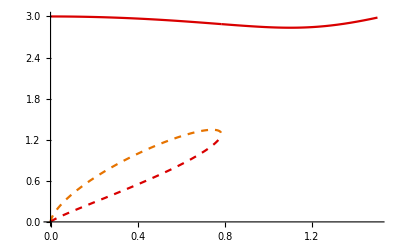

```mathematica
Plot[{HoutLRefftop[ℓ],HoutLReffbottom[ℓ],HinLRefftop[ℓ],HinLReffbottom[ℓ]},{ℓ,0,1.5},PlotStyle->{Darker[Red,0.15],Darker[Red,0.15],{Darker[Orange,0.10],Dashed},{Darker[Red,0.15],Dashed}}]
```

Determination of critical light ring length for the effective geometry

```mathematica
FindRoot[Hroot1[ℓ]==HinLRefftop[ℓ],{ℓ,0.7}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{ℓ→0.783625}

```mathematica
Subscript[ℋLReffℓ, c]=0.7836251476953365;
```

```mathematica
FindMinimum[HoutLReffbottom[ℓ],{ℓ,1}]
```

{2.83552,{ℓ→1.1004}}

```mathematica
FindMinimum[HoutLReffbottom[ℓ],{ℓ,1.05}]
```

FindMinimum::nrnum: The function value Nothing is not a real number at {ℓ} = {22.1044}.

{2.83552,{ℓ→1.1004}}

#### [II.2.2.2] Light rings in the effective geometry: Dynamical behavior

```mathematica
Subscript[dd𝒱, H][r_,M_,ℓ_]=Assuming[{ℓ>0,M>0,r>0},D[Subscript[d𝒱, H][r,M,ℓ],r]//Simplify];
```

```mathematica
D[D[V[r,3,3,2 ℓ^2,(2M ℓ^2)^(1/3)],r],r]
```

L^2 (6/r^4-(36 M r^4)/((r^3+2 M ℓ^2)^3)+(12 M r)/((r^3+2 M ℓ^2)^2))

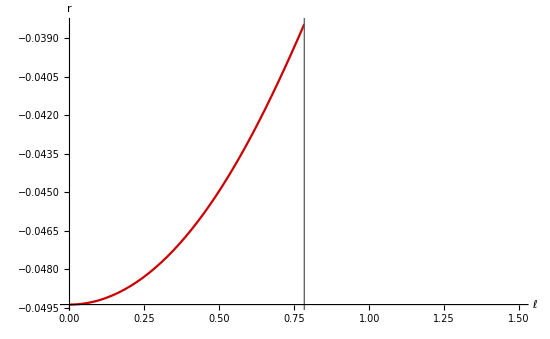

```mathematica
Plot[Subscript[dd𝒱, H][r,M,ℓ]/.{M->1,L->1}/.{r->HoutLRefftop[ℓ]},{ℓ,0,1},PlotRange->{{0,1.5},Automatic},PlotStyle->{Darker[Red,0.2]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->45,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℋLReffℓ, c],0},{Subscript[ℋLReffℓ, c],-1}}]}]
```

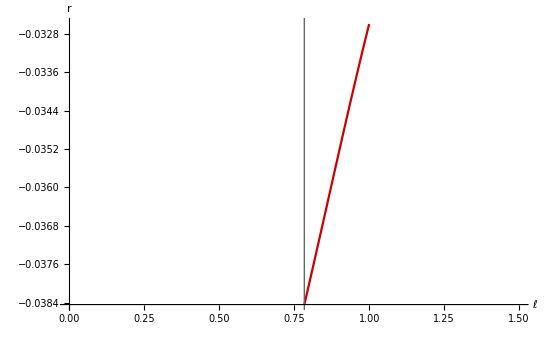

```mathematica
Plot[Subscript[dd𝒱, H][r,M,ℓ]/.{M->1,L->1}/.{r->HoutLReffbottom[ℓ]},{ℓ,0,1},PlotRange->{{0,1.5},Automatic},PlotStyle->{Darker[Red,0.2]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->45,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℋLReffℓ, c],0},{Subscript[ℋLReffℓ, c],-1}}]}]
```

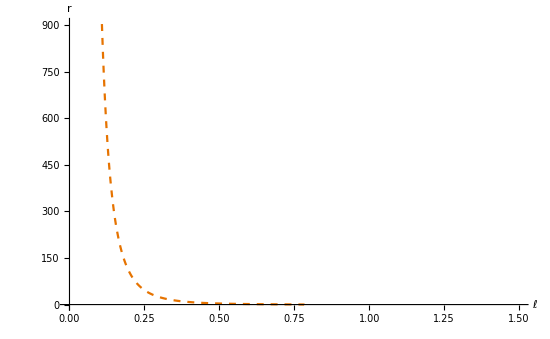

```mathematica
Plot[Subscript[dd𝒱, H][r,M,ℓ]/.{M->1,L->1}/.{r->HinLRefftop[ℓ]},{ℓ,0,1},PlotRange->{{0,1.5},Automatic},PlotStyle->{Darker[Orange,0.1],Dashed},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->55,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℋLReffℓ, c],0},{Subscript[ℋLReffℓ, c],1}}]}]
```

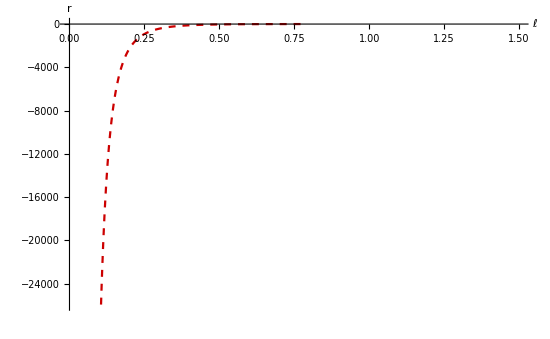

```mathematica
Plot[Subscript[dd𝒱, H][r,M,ℓ]/.{M->1,L->1}/.{r->HinLReffbottom[ℓ]},{ℓ,0,1},PlotRange->{{0,1.5},Automatic},PlotStyle->{Darker[Red,0.2],Dashed},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->55,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[ℋLReffℓ, c],0},{Subscript[ℋLReffℓ, c],-1}}]}]
```

### [II.2.3] Figure 1b: Horizons and light rings

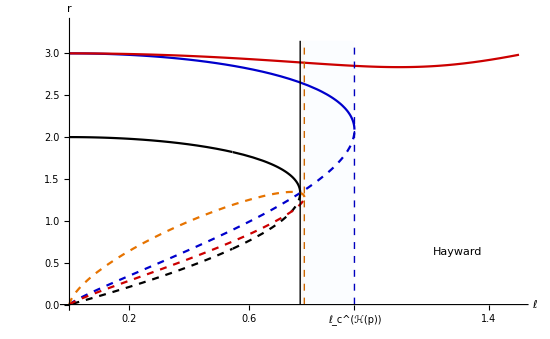

```mathematica
Plot[{SubPlus[rH][1,ℓ],SubMinus[rH][1,ℓ],HoutLRbkg[1,ℓ],HinLRbkg[1,ℓ],HoutLRefftop[ℓ],HoutLReffbottom[ℓ],HinLRefftop[ℓ],HinLReffbottom[ℓ]},{ℓ,0,1.5},PlotStyle->{Black,{Black,Dashed},Darker[Blue,0.2],{Darker[Blue,0.2],Dashed},Darker[Red,0.2],Darker[Red,0.2],{Darker[Orange,0.10],Dashed},{Darker[Red,0.2],Dashed}},PlotRange->{{0,1.5},{0,3.35}},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],Ticks->{{0.2,0.4,0.6,{Subscript[ℋℓ, c],"ℓ_c^ℋ"},{Subscript[ℋbkgℓ𝓅, c],"ℓ_c^(<ℋ(p)>)"},{1.2,"1.2"},{1.4,"1.4"},{1.6,"1.6"},{1.8,"1.8"}},Automatic},TicksStyle->Directive[FontSize->13],ImageSize->550,Prolog->{Opacity[0.10,LightBlue],Rectangle[{Subscript[ℋℓ, c],0},{Subscript[ℋbkgℓ𝓅, c],3.15}],Opacity[0.15,LightOrange],Rectangle[{Subscript[ℋℓ, c],0},{Subscript[ℋLReffℓ, c],3.15}]},Epilog->{Inset[Framed["Hayward",RoundingRadius->2],Scaled[{0.85,0.20}]],{Directive[Thickness->0.0013,Darker[Black,0.2]],Line[{{Subscript[ℋℓ, c],0},{Subscript[ℋℓ, c],3.15}}]},{Directive[Thickness->0.0011,Darker[Orange,0.2],Dashed],Line[{{Subscript[ℋLReffℓ, c],0},{Subscript[ℋLReffℓ, c],3.15}}]},{Directive[Thickness->0.0013,Darker[Blue,0.25],Dashed],Line[{{Subscript[ℋbkgℓ𝓅, c],0},{Subscript[ℋbkgℓ𝓅, c],3.15}}]}}]
```

### [II.2.4] Figure 2b: Difference between the outer LR in the effective vs. outer LR in the background geometry

```mathematica
HLRdiff1[ℓ_]:=HoutLRefftop[ℓ]-HoutLRbkg[1,ℓ];
```

```mathematica
HLRdiff2[ℓ_]:=HoutLReffbottom[ℓ]-HoutLRbkg[1,ℓ];
```

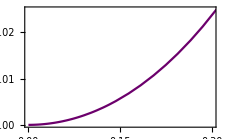

```mathematica
ℋdiffSmallℓ=Plot[{HLRdiff1[ℓ]},{ℓ,0,1},PlotStyle->{Darker[Purple,0.15],Darker[Purple,0.15]},PlotRange->{{0,0.30},{0,0.025}},Frame->True,ImageSize->225]
```

Scaling behavior in the limit ℓ->0

```mathematica
Limit[D[HLRdiff1[ℓ],ℓ],ℓ->0]
```

0

```mathematica
Limit[D[D[HLRdiff1[ℓ],ℓ],ℓ],ℓ->0]/2
```

1/4

```mathematica
Limit[D[D[D[HLRdiff1[ℓ],ℓ],ℓ],ℓ],ℓ->0]/6
```

0

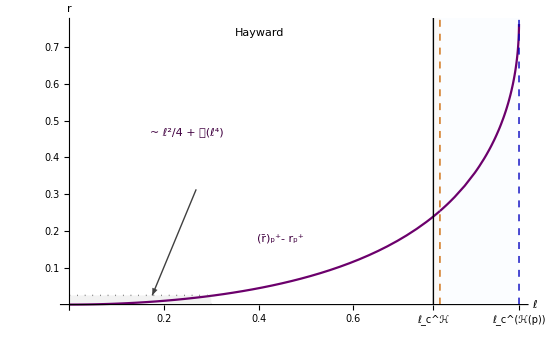

```mathematica
Plot[{HLRdiff1[ℓ],HLRdiff2[ℓ]},{ℓ,0,1},PlotStyle->{Darker[Purple,0.15],Darker[Purple,0.15]},PlotRange->{{0,1.15},{All,0.775}},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],Ticks->{{0.2,0.4,0.6,{Subscript[ℋℓ, c],"ℓ_c^ℋ"},{Subscript[ℋbkgℓ𝓅, c],"ℓ_c^(<ℋ(p)>)"},{1.1,"1.1"}},{0.1,0.2,0.3,0.4,0.5,0.6,0.7}},TicksStyle->Directive[FontSize->13],ImageSize->550,Prolog->{Opacity[0.10,Gray],Rectangle[{0,0},{0.30,0.025}],Opacity[0.10,LightBlue],Rectangle[{Subscript[ℋℓ, c],0},{Subscript[ℋbkgℓ𝓅, c],3.115}],Opacity[0.15,LightOrange],Rectangle[{Subscript[ℋℓ, c],0},{Subscript[ℋLReffℓ, c],3.115}]},Epilog->{Inset[ℋdiffSmallℓ,Scaled[{0.30,0.60}]],Inset[Framed["Hayward",RoundingRadius->2],Scaled[{0.425,0.95}]],Inset[Style["(r̄)_p^(<+>)- r_p^(<+>)",Darker[Purple,0.50]],Scaled[{0.47,0.245}]],Inset[Style["~ ℓ^2/4 + 𝒪(ℓ^4)",Darker[Purple,0.50]],Scaled[{0.27,0.61}]],{Directive[Thickness->0.0013,Darker[Gray,0.5]],Arrowheads[0.03],Arrow[{{0.268,0.313},{0.175,0.025}}]},
{Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{0,0.025},{0.30,0.025}}]},{Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{0.30,0},{0.30,0.025}}]},{Directive[Thickness->0.0013,Darker[Black,0.2]],Line[{{Subscript[ℋℓ, c],0},{Subscript[ℋℓ, c],1}}]},{Directive[Thickness->0.0011,Darker[Orange,0.2],Dashed],Line[{{Subscript[ℋLReffℓ, c],0},{Subscript[ℋLReffℓ, c],1}}]},{Directive[Thickness->0.0013,Darker[Blue,0.25],Dashed],Line[{{Subscript[ℋbkgℓ𝓅, c],0},{Subscript[ℋbkgℓ𝓅, c],1}}]}}]
```

## [II.3] Phase velocities

#### First- and second-order derivatives of NED Lagrangian density [Eqs. (6.17) and (6.18)]

```mathematica
Assuming[{r>0,M>0,ℓ>0},D[ℒ[ℱ,3,3,2 ℓ^2],ℱ]/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->(M^(2/3)ℓ^(1/3))/2^(1/3)}//Simplify]
```

(18 2^(2/3) M^(2/3) r^7 ℓ^(4/3))/((r^3+2 M ℓ^2)^3)

```mathematica
Assuming[{r>0,M>0,ℓ>0},D[D[ℒ[ℱ,3,3,2 ℓ^2],ℱ],ℱ]/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->(M^(2/3)ℓ^(1/3))/2^(1/3)}//Simplify]
```

(9 2^(1/3) r^11 (ℓ/M)^(2/3) (r^3-7 M ℓ^2))/((r^3+2 M ℓ^2)^4)

#### Phase velocities in the background and effective geometry [Eqs. (6.19) and (6.20)]

```mathematica
√(Subscript[f, H][r])
```

√(1-(2 M r^2)/(r^3+2 M ℓ^2))

```mathematica
ℋ𝒷𝓀ℊvph[r_,M_,ℓ_]:=√(1-(2 M r^2)/(r^3+2 M ℓ^2));
```

```mathematica
Assuming[{r>0,M>0,ℓ>0},√(Subscript[f, H][r](1+(2ℱ[r] D[D[ℒ[ℱ,3,3,2 ℓ^2],ℱ],ℱ])/D[ℒ[ℱ,3,3,2 ℓ^2],ℱ] Sin[η]^2))/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->(M^(2/3)ℓ^(1/3))/2^(1/3)}//Simplify]
```

√(((-2 M r^2+r^3+2 M ℓ^2) (r^3+2 M ℓ^2+(r^3-7 M ℓ^2) Sin[η]^2))/((r^3+2 M ℓ^2)^2))

```mathematica
ℋℯ𝒻𝒻vph[r_,M_,ℓ_,η_]:=√(((-2 M r^2+r^3+2 M ℓ^2) (r^3+2 M ℓ^2+(r^3-7 M ℓ^2) Sin[η]^2))/((r^3+2 M ℓ^2)^2));
```

```mathematica
Assuming[{r>0,M>0,ℓ>0},(1+(2ℱ[r] D[D[ℒ[ℱ,3,3,2 ℓ^2],ℱ],ℱ])/D[ℒ[ℱ,3,3,2 ℓ^2],ℱ] Sin[η]^2)/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->(M^(2/3)ℓ^(1/3))/2^(1/3)}//Simplify]
```

(r^3+2 M ℓ^2+(r^3-7 M ℓ^2) Sin[η]^2)/(r^3+2 M ℓ^2)

```mathematica
((r^3+2 M ℓ^2+(r^3-7 M ℓ^2) Sin[η]^2)/(r^3+2 M ℓ^2))-(1+(r^3-7 M ℓ^2)/(r^3+2 M ℓ^2)Sin[η]^2)//Simplify
```

0

## [III] Cadoni et al. model [Sec. IV.3]

#### Metric function f_C(r) [Eq. (4.21)]

```mathematica
Subscript[f, C][r_]:=f[r,3,1,ℓ^3/M,ℓ]
```

```mathematica
Subscript[f, C][r]
```

1-(2 M r^2)/(r+ℓ)^3

## [III.1] Horizon locations and critical length

```mathematica
Solve[Subscript[f, C][r]==0,r]//Simplify
```

{{r→1/3 (2 M-3 ℓ+(4 M (M-3 ℓ))/((8 M^3-36 M^2 ℓ+27 M ℓ^2+3 √3 √(-M^2 (8 M-27 ℓ) ℓ^3))^(1/3))+(8 M^3-36 M^2 ℓ+27 M ℓ^2+3 √3 √(-M^2 (8 M-27 ℓ) ℓ^3))^(1/3))},{r→1/6 (4 M-6 ℓ-(4 ⅈ (-ⅈ+√3) M (M-3 ℓ))/((8 M^3-36 M^2 ℓ+27 M ℓ^2+3 √3 √(-M^2 (8 M-27 ℓ) ℓ^3))^(1/3))+ⅈ (ⅈ+√3) (8 M^3-36 M^2 ℓ+27 M ℓ^2+3 √3 √(-M^2 (8 M-27 ℓ) ℓ^3))^(1/3))},{r→1/6 (4 M-6 ℓ+(4 ⅈ (ⅈ+√3) M (M-3 ℓ))/((8 M^3-36 M^2 ℓ+27 M ℓ^2+3 √3 √(-M^2 (8 M-27 ℓ) ℓ^3))^(1/3))-(1+ⅈ √3) (8 M^3-36 M^2 ℓ+27 M ℓ^2+3 √3 √(-M^2 (8 M-27 ℓ) ℓ^3))^(1/3))}}

```mathematica
SubPlus[rC][M_,ℓ_]=Solve[Subscript[f, C][r]==0,r][[1,1,2]];
```

```mathematica
SubMinus[rC][M_,ℓ_]=Solve[Subscript[f, C][r]==0,r][[3,1,2]];
```

#### Series expansions of horizons about ℓ = 0 [Eqs. (4.25) and (4.26)]

```mathematica
Assuming[{M>0,ℓ>0},Series[SubPlus[rC][M,ℓ],{ℓ,0,4}]//Simplify]
```

2 M-3 ℓ-(3 ℓ^2)/(2 M)-(5 ℓ^3)/(2 M^2)-(21 ℓ^4)/(4 M^3)+O[ℓ]^(9/2)

```mathematica
Assuming[{M>0,ℓ>0},Series[SubMinus[rC][M,ℓ],{ℓ,0,4}]//Simplify]
```

ℓ^(3/2)/(√2 √M)+(3 ℓ^2)/(4 M)+(21 ℓ^(5/2))/(16 √2 M^(3/2))+(5 ℓ^3)/(4 M^2)+(1287 ℓ^(7/2))/(512 √2 M^(5/2))+(21 ℓ^4)/(8 M^3)+O[ℓ]^(9/2)

#### Critical length [Eq. (4.27)]

```mathematica
Solve[D[Subscript[f, C][r],r]==0/.{r->SubPlus[rC][M,ℓ]} ,ℓ]
```

{{ℓ→(8 M)/27}}

```mathematica
Solve[SubPlus[rC][M,ℓ]==SubMinus[rC][M,ℓ],ℓ]
```

{{ℓ→0},{ℓ→(8 M)/27}}

```mathematica
Subscript[𝒞ℓ, c]=8/27;
```

#### Effective metric tensor components [Eqs. (4.29) and (4.30)]

```mathematica
Assuming[{α>0,r>0,M>0,ℓ>0},1+(2ℱ[r] D[D[ℒ[ℱ,3,1,ℓ^3/M],ℱ],ℱ])/D[ℒ[ℱ,3,1,ℓ^3/M],ℱ]/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify]
```

(2 r-3 ℓ)/(2 (r+ℓ))

```mathematica
((2 r-3 ℓ)/(2 (r+ℓ)))-(1-(5ℓ)/(2(r+ℓ)))//Simplify
```

0

## [III.2] Light rings

### [III.2.1] Light rings in the background geometry

#### [III.2.1.1] Light rings in the background geometry: Locations and critical length

Potential in the background geometry [Eq. (5.11)]

```mathematica
V[r,3,1,ℓ^3/M,ℓ]
```

-En^2+L^2 (1/r^2-(2 M)/(r+ℓ)^3)

```mathematica
Solve[D[V[r,3,1,ℓ^3/M,ℓ],r]==0,r]//Simplify;
```

Identification of the physically relevant roots that represent the inner and outer light ring in the Cadoni et al. RBH model’s background geometry.
The fourth [third] root corresponds to the outer [inner] light ring.

```mathematica
CoutLRbkg[M_,ℓ_]:=Simplify[Solve[D[V[r,3,1,ℓ^3/M,ℓ],r]==0,r][[4,1,2]]];
```

```mathematica
CinLRbkg[M_,ℓ_]:=Simplify[Solve[D[V[r,3,1,ℓ^3/M,ℓ],r]==0,r][[3,1,2]]];
```

#### Series expansions of light rings about ℓ = 0 in the background geometry[Eqs. (5.15) and (5.16)]

```mathematica
Series[CoutLRbkg[M,ℓ],{ℓ,0,3},Assumptions->{M>0,ℓ>0}]
```

3 M-4 ℓ-(2 ℓ^2)/M-(28 ℓ^3)/(9 M^2)+O[ℓ]^(10/3)

```mathematica
Series[CinLRbkg[M,ℓ],{ℓ,0,3},Assumptions->{M>0,ℓ>0}]
```

ℓ^(4/3)/(3^(1/3) M^(1/3))+(4 ℓ^(5/3))/(3 3^(2/3) M^(2/3))+(2 ℓ^2)/(3 M)+(260 ℓ^(7/3))/(243 3^(1/3) M^(4/3))+(1309 ℓ^(8/3))/(729 3^(2/3) M^(5/3))+(28 ℓ^3)/(27 M^2)+O[ℓ]^(10/3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

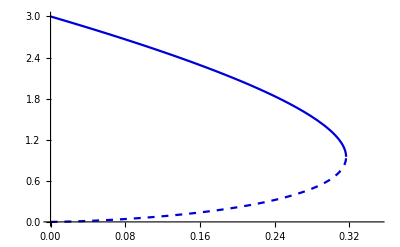

```mathematica
Plot[{CoutLRbkg[1,ℓ],CinLRbkg[1,ℓ]},{ℓ,0,0.35},PlotStyle->{Darker[Blue,0.15],{Darker[Blue,0.15],Dashed}}]
```

```mathematica
FindRoot[CoutLRbkg[1,ℓ]==CinLRbkg[1,ℓ],{ℓ,0.3}]
```

{ℓ→0.316406}

```mathematica
Subscript[𝒞bkgℓ𝓅, c]=0.31640625;
```

#### [III.2.1.2] Light rings in the background geometry: Dynamical behavior

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

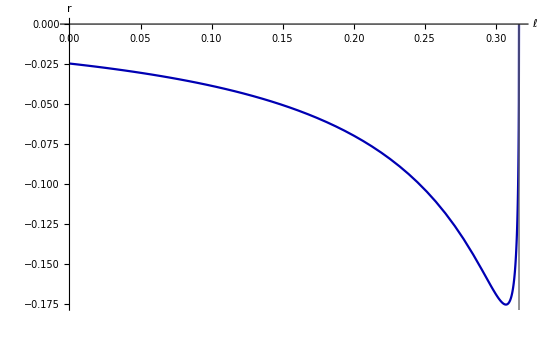

```mathematica
Plot[D[D[V[r,3,1,ℓ^3/M,ℓ],r],r]/.{M->1,L->1}/.{r->CoutLRbkg[1,ℓ]},{ℓ,0,Subscript[𝒞bkgℓ𝓅, c]},PlotRange->Automatic,PlotStyle->{Darker[Blue,0.3]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImagePadding->47,ImageSize->550,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[𝒞bkgℓ𝓅, c],0},{Subscript[𝒞bkgℓ𝓅, c],-1}}]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

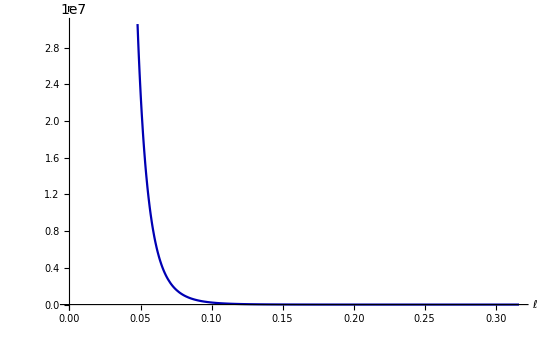

```mathematica
Plot[D[D[V[r,3,1,ℓ^3/M,ℓ],r],r]/.{M->1,L->1}/.{r->CinLRbkg[1,ℓ]},{ℓ,0,Subscript[𝒞bkgℓ𝓅, c]},PlotRange->Automatic,PlotStyle->{Darker[Blue,0.3]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImagePadding->47,ImageSize->550,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[𝒞bkgℓ𝓅, c],0},{Subscript[𝒞bkgℓ𝓅, c],1}}]}]
```

### [III.2.2] Light rings in the effective geometry

#### [III.2.2.1] Light rings in the effective geometry: Locations and critical length

```mathematica
Subscript[𝒱, C][r_,M_,ℓ_]:=𝒱[r,3,1,ℓ^3/M,ℓ]/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify
```

Potential in the background geometry [Eq. (5.14)]

```mathematica
Assuming[{ℓ>0,M>0,r>0},Subscript[𝒱, C][r,M,ℓ]//FullSimplify]
```

-En^2+(L^2 (2 r-3 ℓ) (-2 M r^2+(r+ℓ)^3))/(2 r^2 (r+ℓ)^4)

```mathematica
Subscript[d𝒱, C][r_,M_,ℓ_]=Assuming[{ℓ>0,M>0,r>0},D[Subscript[𝒱, C][r,M,ℓ],r]//Simplify];
```

```mathematica
Solve[Subscript[d𝒱, C][r,M,ℓ]==0,r]/.{M->1}//Simplify
```

{{r→Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,1]},{r→Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,2]},{r→Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,3]},{r→Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,4]},{r→Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,5]}}

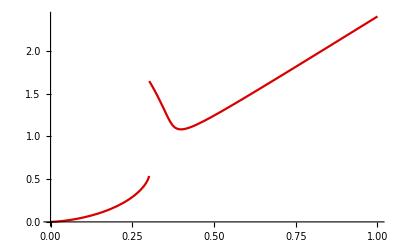

```mathematica
Plot[Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,1],{ℓ,0,1},PlotStyle->{Darker[Red,0.15]}]
```

```mathematica
Croot1[ℓ_]:=Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,1];
```

```mathematica
CinLReffbottom[ℓ_]:=If[Croot1[ℓ]<0.8,Croot1[ℓ],Nothing];
```

```mathematica
CoutLReffbottom[ℓ_]:=If[Croot1[ℓ]>0.8,Croot1[ℓ],Nothing];
```

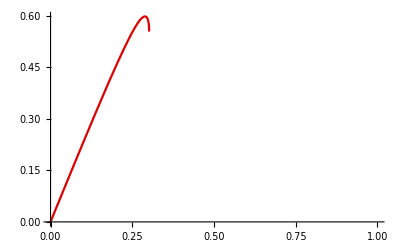

```mathematica
Plot[Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,2],{ℓ,0,1},PlotStyle->{Darker[Red,0.15]}]
```

```mathematica
CinLRefftop[ℓ_]:=Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,2];
```

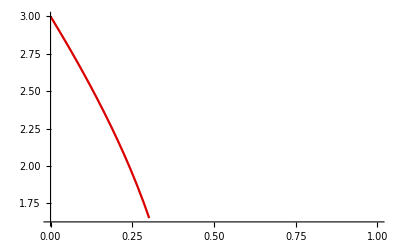

```mathematica
Plot[Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,3],{ℓ,0,1},PlotStyle->{Darker[Red,0.15]}]
```

```mathematica
CoutLRefftop[ℓ_]:=Root[-6 ℓ^5-25 ℓ^4 #1-35 ℓ^3 #1^2+(28 ℓ-15 ℓ^2) #1^3+(-12+5 ℓ) #1^4+4 #1^5&,3];
```

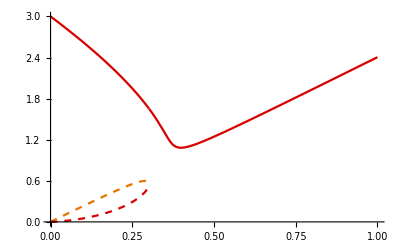

```mathematica
Plot[{CoutLRefftop[ℓ],CoutLReffbottom[ℓ],CinLRefftop[ℓ],CinLReffbottom[ℓ]},{ℓ,0,1.},PlotStyle->{Darker[Red,0.15],Darker[Red,0.15],{Darker[Orange,0.10],Dashed},{Darker[Red,0.15],Dashed}}]
```

Determination of critical light ring length for the effective geometry

```mathematica
FindRoot[Croot1[ℓ]==CinLRefftop[ℓ],{ℓ,0.25}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{ℓ→0.301636}

```mathematica
Subscript[𝒞LReffℓ, c]=0.30163610420594855;
```

```mathematica
FindMinimum[CoutLReffbottom[ℓ],{ℓ,0.38}]
```

{1.08343,{ℓ→0.399057}}

```mathematica
FindMinimum[CoutLReffbottom[ℓ],{ℓ,0.39}]
```

{1.08343,{ℓ→0.399057}}

#### [III.2.2.2] Light rings in the effective geometry: Dynamical behavior

```mathematica
Subscript[dd𝒱, C][r_,M_,ℓ_]=Assuming[{ℓ>0,M>0,r>0},D[Subscript[d𝒱, C][r,M,ℓ],r]//Simplify];
```

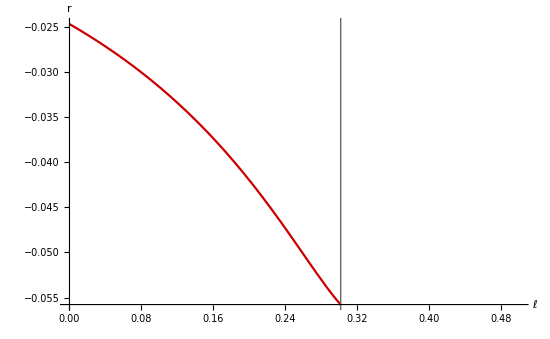

```mathematica
Plot[Subscript[dd𝒱, C][r,M,ℓ]/.{M->1,L->1}/.{r->CoutLRefftop[ℓ]},{ℓ,0,0.5},PlotRange->{{0,0.5},Automatic},PlotStyle->{Darker[Red,0.2]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->45,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[𝒞LReffℓ, c],0},{Subscript[𝒞LReffℓ, c],-1}}]}]
```

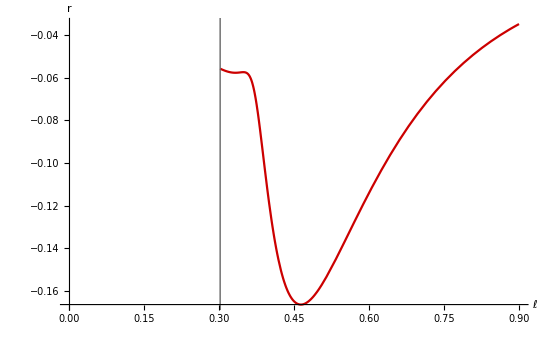

```mathematica
Plot[Subscript[dd𝒱, C][r,M,ℓ]/.{M->1,L->1}/.{r->CoutLReffbottom[ℓ]},{ℓ,0,0.9},PlotRange->{{0,0.9},Automatic},PlotStyle->{Darker[Red,0.2]},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->45,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[𝒞LReffℓ, c],0},{Subscript[𝒞LReffℓ, c],-1}}]}]
```

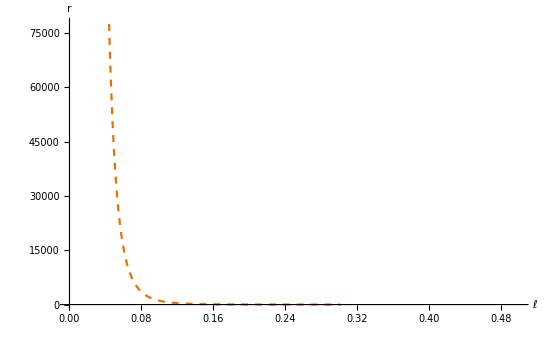

```mathematica
Plot[Subscript[dd𝒱, C][r,M,ℓ]/.{M->1,L->1}/.{r->CinLRefftop[ℓ]},{ℓ,0,0.5},PlotRange->{{0,0.5},Automatic},PlotStyle->{Darker[Orange,0.1],Dashed},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->45,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[𝒞LReffℓ, c],0},{Subscript[𝒞LReffℓ, c],1}}]}]
```

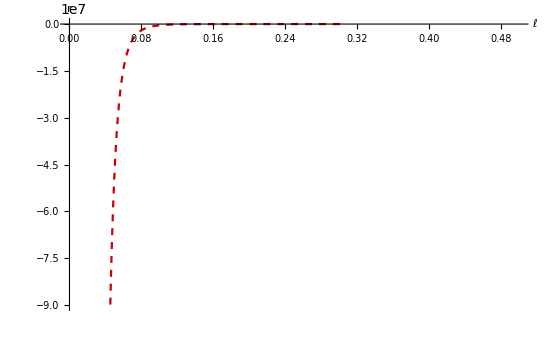

```mathematica
Plot[Subscript[dd𝒱, C][r,M,ℓ]/.{M->1,L->1}/.{r->CinLReffbottom[ℓ]},{ℓ,0,0.5},PlotRange->{{0,0.5},Automatic},PlotStyle->{Darker[Red,0.2],Dashed},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],TicksStyle->Directive[FontSize->11],ImageSize->550,ImagePadding->45,Epilog->{Directive[Thickness->0.0015,Darker[Gray,0.2]],Line[{{Subscript[𝒞LReffℓ, c],0},{Subscript[𝒞LReffℓ, c],-1}}]}]
```

### [III.2.3] Figure 1c: Horizons and light rings

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

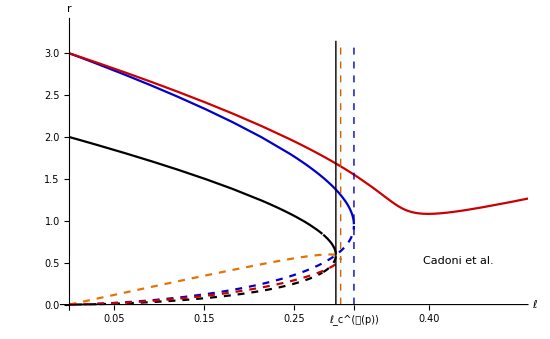

```mathematica
Plot[{SubPlus[rC][1,ℓ],SubMinus[rC][1,ℓ],CoutLRbkg[1,ℓ],CinLRbkg[1,ℓ],CoutLRefftop[ℓ],CoutLReffbottom[ℓ],CinLRefftop[ℓ],CinLReffbottom[ℓ]},{ℓ,0,1.5},PlotStyle->{Black,{Black,Dashed},Darker[Blue,0.2],{Darker[Blue,0.2],Dashed},Darker[Red,0.2],Darker[Red,0.2],{Darker[Orange,0.10],Dashed},{Darker[Red,0.2],Dashed}},PlotRange->{{0,0.5},{0,3.35}},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],Ticks->{{{0.05,"0.05"},{0.10,"0.10"},{0.15,"0.15"},{0.20,"0.20"},{0.25,"0.25"},{Subscript[𝒞ℓ, c],"ℓ_c^𝒞"},{Subscript[𝒞bkgℓ𝓅, c]," ℓ_c^(<𝒞(p)>)"},{0.35,"0.35"},{0.40,"0.40"},{0.45,"0.45"}},Automatic},TicksStyle->Directive[FontSize->13],ImageSize->550,Prolog->{Opacity[0.10,LightBlue],Rectangle[{Subscript[𝒞ℓ, c],0},{Subscript[𝒞bkgℓ𝓅, c],3.15}],Opacity[0.15,LightOrange],Rectangle[{Subscript[𝒞ℓ, c],0},{Subscript[𝒞LReffℓ, c],3.15}]},Epilog->{Inset[Framed["Cadoni et al.",RoundingRadius->2],Scaled[{0.85,0.17}]],{Directive[Thickness->0.0013,Darker[Black,0.2]],Line[{{Subscript[𝒞ℓ, c],0},{Subscript[𝒞ℓ, c],3.15}}]},{Directive[Thickness->0.0011,Darker[Orange,0.2],Dashed],Line[{{Subscript[𝒞LReffℓ, c],0},{Subscript[𝒞LReffℓ, c],3.15}}]},{Directive[Thickness->0.0013,Darker[Blue,0.25],Dashed],Line[{{Subscript[𝒞bkgℓ𝓅, c],0},{Subscript[𝒞bkgℓ𝓅, c],3.15}}]}}]
```

### [II.2.4] Figure 2c: Difference between the outer LR in the effective vs. outer LR in the background geometry

```mathematica
CLRdiff1[ℓ_]:=CoutLRefftop[ℓ]-CoutLRbkg[1,ℓ];
```

```mathematica
CLRdiff2[ℓ_]:=CoutLReffbottom[ℓ]-CoutLRbkg[1,ℓ];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

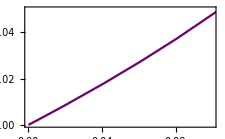

```mathematica
𝒞diffSmallℓ=Plot[{CLRdiff1[ℓ]},{ℓ,0,1},PlotStyle->{Darker[Purple,0.15],Darker[Purple,0.15]},PlotRange->{{0,0.1},{0,0.05}},Frame->True,ImageSize->225]
```

Scaling behavior in the limit ℓ->0

```mathematica
Limit[D[CLRdiff1[ℓ],ℓ],ℓ->0]
```

5/12

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

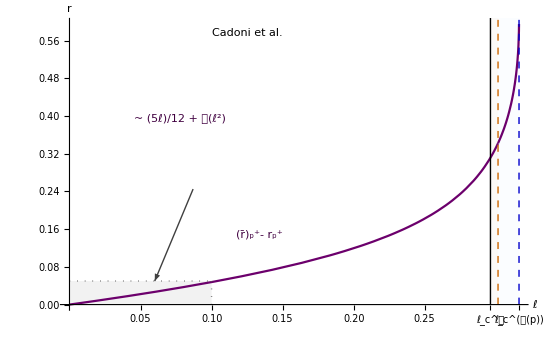

```mathematica
Plot[{CLRdiff1[ℓ],CLRdiff2[ℓ]},{ℓ,0,1},PlotStyle->{Darker[Purple,0.15],Darker[Purple,0.15]},PlotRange->{{0,0.365},{All,0.595}},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],Ticks->{{{0.05,"0.05"},{0.10,"0.10"},{0.15,"0.15"},{0.20,"0.20"},{0.25,"0.25"},{Subscript[𝒞ℓ, c],"ℓ_c^𝒞"},{Subscript[𝒞bkgℓ𝓅, c]," ℓ_c^(<𝒞(p)>)"}},Automatic},TicksStyle->Directive[FontSize->13],ImageSize->550,Prolog->{Opacity[0.10,Gray],Rectangle[{0,0},{0.10,0.05}],Opacity[0.10,LightBlue],Rectangle[{Subscript[𝒞ℓ, c],0},{Subscript[𝒞bkgℓ𝓅, c],3.115}],Opacity[0.15,LightOrange],Rectangle[{Subscript[𝒞ℓ, c],0},{Subscript[𝒞LReffℓ, c],3.15}]},Epilog->{Inset[𝒞diffSmallℓ,Scaled[{0.30,0.60}]],Inset[Framed["Cadoni et al.",RoundingRadius->2],Scaled[{0.40,0.95}]],Inset[Style["(r̄)_p^(<+>)- r_p^(<+>)",Darker[Purple,0.50]],Scaled[{0.425,0.26}]],Inset[Style["~ (5ℓ)/12 + 𝒪(ℓ^2)",Darker[Purple,0.50]],Scaled[{0.255,0.66}]],{Directive[Thickness->0.0013,Darker[Gray,0.5]],Arrowheads[0.03],Arrow[{{0.087,0.245},{0.06,0.05}}]},
{Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{0,0.05},{0.10,0.05}}]},{Directive[Thickness->0.0015,Darker[Gray,0.3],Dotted],Line[{{0.10,0},{0.10,0.05}}]},{Directive[Thickness->0.0013,Darker[Black,0.2]],Line[{{Subscript[𝒞ℓ, c],0},{Subscript[𝒞ℓ, c],1}}]},{Directive[Thickness->0.0011,Darker[Orange,0.2],Dashed],Line[{{Subscript[𝒞LReffℓ, c],0},{Subscript[𝒞LReffℓ, c],1}}]},{Directive[Thickness->0.0013,Darker[Blue,0.2],Dashed],Line[{{Subscript[𝒞bkgℓ𝓅, c],0},{Subscript[𝒞bkgℓ𝓅, c],1}}]}}]
```

## [III.3] Phase velocities

#### First- and second-order derivatives of NED Lagrangian density [Eq. (6.5)]

```mathematica
Assuming[{r>0,M>0,ℓ>0},D[ℒ[ℱ,3,1,ℓ^3/M],ℱ]/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify]
```

(12 r^5)/(r+ℓ)^5

```mathematica
Assuming[{r>0,M>0,ℓ>0},D[D[ℒ[ℱ,3,1,ℓ^3/M],ℱ],ℱ]/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify]
```

-(15 r^9)/(M (r+ℓ)^6)

#### Phase velocities in the background and effective geometry [Eqs. (6.6) and (6.7)]

```mathematica
√(Subscript[f, C][r])
```

√(1-(2 M r^2)/(r+ℓ)^3)

```mathematica
𝒞𝒷𝓀ℊvph[r_,M_,ℓ_]:=√(1-(2 M r^2)/(r+ℓ)^3);
```

```mathematica
Assuming[{r>0,M>0,ℓ>0},√(Subscript[f, C][r](1+(2ℱ[r] D[D[ℒ[ℱ,3,1,ℓ^3/M],ℱ],ℱ])/D[ℒ[ℱ,3,1,ℓ^3/M],ℱ] Sin[η]^2))/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify]
```

1/2 √(((-2 M r^2+(r+ℓ)^3) (4 r-ℓ+5 ℓ Cos[2 η]))/(r+ℓ)^4)

```mathematica
𝒞ℯ𝒻𝒻vph[r_,M_,ℓ_,η_]:=1/2 √(((-2 M r^2+(r+ℓ)^3) (4 r-ℓ+5 ℓ Cos[2 η]))/(r+ℓ)^4);
```

```mathematica
Assuming[{r>0,M>0,ℓ>0},(1+(2ℱ[r] D[D[ℒ[ℱ,3,1,ℓ^3/M],ℱ],ℱ])/D[ℒ[ℱ,3,1,ℓ^3/M],ℱ] Sin[η]^2)/.{ℱ->ℱ[r]}/.{Subscript[Q, m]->√((M ℓ)/2)}//Simplify]
```

1-(5 ℓ Sin[η]^2)/(2 (r+ℓ))

### [III.3.2] Figure 3: η-dependence of the phase velocity in the effective metric

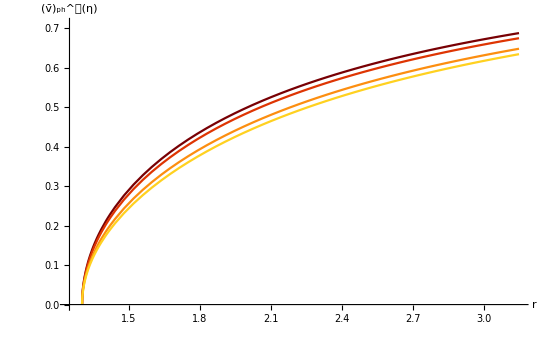

```mathematica
Plot[{𝒞ℯ𝒻𝒻vph[r,1,0.2,0],𝒞ℯ𝒻𝒻vph[r,1,0.2,π/6],𝒞ℯ𝒻𝒻vph[r,1,0.2,π/3],𝒞ℯ𝒻𝒻vph[r,1,0.2,π/2]},{r,1.25,3.15},PlotStyle->"SolarColors",PlotRange->{{1.25,3.15},{0,0.71}},AxesLabel->{"r","(v̄)_ph^(<𝒞>)(η)"},AxesStyle->Arrowheads[{0.00,0.03}],TicksStyle->Directive[FontSize->12],ImageSize->550,Epilog->Inset[Framed[LineLegend["SolarColors",{" η = 0"," η = π/6"," η = π/3"," η = π/2"}],RoundingRadius->1],Scaled[{0.66,0.35}]]]
```

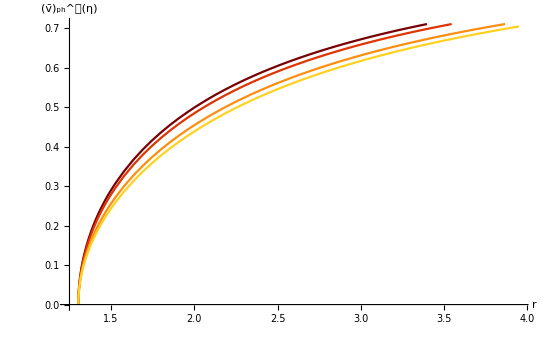

```mathematica
Plot[{𝒞ℯ𝒻𝒻vph[r,1,0.2,0],𝒞ℯ𝒻𝒻vph[r,1,0.2,π/6],𝒞ℯ𝒻𝒻vph[r,1,0.2,π/3],𝒞ℯ𝒻𝒻vph[r,1,0.2,π/2]},{r,1.25,3.95},PlotStyle->"SolarColors",PlotRange->{{1.25,3.95},{0,0.71}},AxesLabel->{"r","(v̄)_ph^(<𝒞>)(η)"},AxesStyle->Arrowheads[{0.00,0.03}],TicksStyle->Directive[FontSize->12],ImageSize->550,Epilog->Inset[Framed[LineLegend["SolarColors",{" η = 0"," η = π/6"," η = π/3"," η = π/2"}],RoundingRadius->1],Scaled[{0.66,0.35}]]]
```

### [III.3.2] Figure 4: Comparison of phase velocities in the Cadoni et al. model to the Schwarzschild case

```mathematica
𝒞ℯ𝒻𝒻vph[r,M,ℓ,η]
```

1/2 √(((-2 M r^2+(r+ℓ)^3) (4 r-ℓ+5 ℓ Cos[2 η]))/(r+ℓ)^4)

```mathematica
𝒞𝒷𝓀ℊvph[r,M,ℓ]
```

√(1-(2 M r^2)/(r+ℓ)^3)

```mathematica
{1/2 √(((4 r-6 ℓ) (-2 r^2+(r+ℓ)^3))/(r+ℓ)^4),√(1-(2 r^2)/(r+ℓ)^3),√(1-2/r)}/.{ℓ->Subscript[𝒞ℓ, c]}//Simplify
```

{1/2 √(((-16/9+4 r) (-2 r^2+(8/27+r)^3))/(8/27+r)^4),√(1-(2 r^2)/(8/27+r)^3),√((-2+r)/r)}

```mathematica
N[Solve[1/2 √(((-16/9+4 r) (-2 r^2+(8/27+r)^3))/(8/27+r)^4)==√((-2+r)/r),r]//Simplify]
```

{{r→-0.0977837-0.184438 ⅈ},{r→-0.0977837+0.184438 ⅈ},{r→-0.124636},{r→3.83131}}

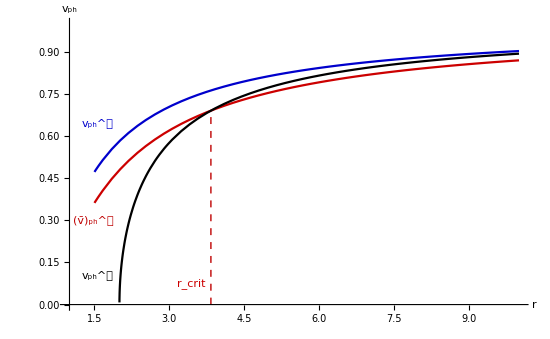

```mathematica
Plot[{√(1-(2 r^2)/(8/27+r)^3),1/2 √(((-16/9+4 r) (-2 r^2+(8/27+r)^3))/(8/27+r)^4),√((-2+r)/r)},{r,1.5,10},PlotStyle->{Darker[Blue,0.20],Darker[Red,0.20],Black},PlotRange->{{1,10},{0,1}},AxesLabel->{"r","v_ph"},AxesStyle->Arrowheads[{0.00,0.03}],TicksStyle->Directive[FontSize->12],ImageSize->550,Epilog->{Inset[Style["v_ph^(<𝒞>)",Darker[Blue,0.20]],Scaled[{0.08,0.64}]],Inset[Style["(v̄)_ph^(<𝒞>)",Darker[Red,0.25]],Scaled[{0.07,0.31}]],Inset[Style["v_ph^(<𝒮>)",Black],Scaled[{0.080,0.12}]],Inset[Style["r_crit",Darker[Red,0.2]],Scaled[{0.28,0.09}]],{Directive[Thickness->0.002,Darker[Red,0.25],Dashed],Line[{{3.8313148721317374,0},{3.8313148721317374,0.6913653161921898}}]}}]
```

## [IV] Comparison of RBH models

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::munfl: (1.95068×10^-6)^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.95068×10^-6)^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.95068×10^-6)^72 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

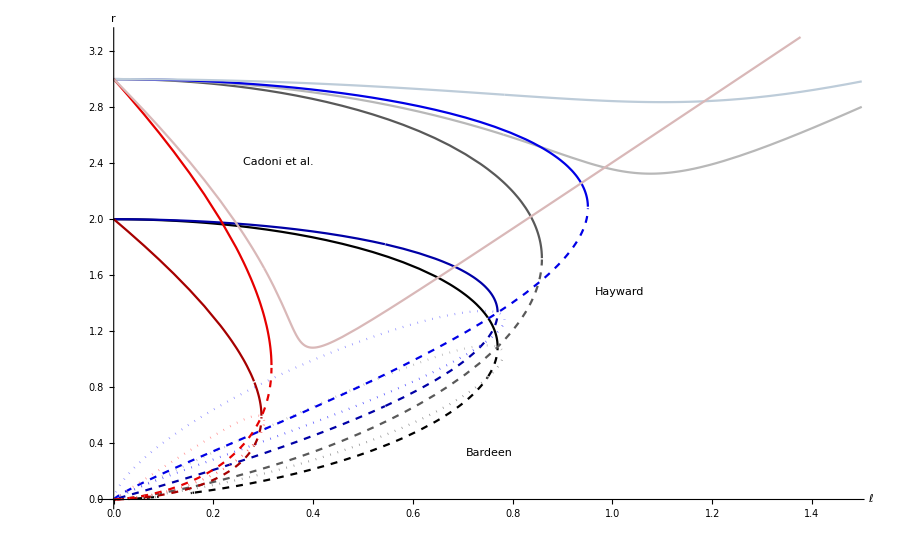

```mathematica
Plot[{SubPlus[rB][1,ℓ],SubMinus[rB][1,ℓ],BoutLRbkg[1,ℓ],BinLRbkg[1,ℓ],BoutLRefftop[ℓ],BoutLReffbottom[ℓ],BinLRefftop[ℓ],BinLReffbottom[ℓ],SubPlus[rH][1,ℓ],SubMinus[rH][1,ℓ],HoutLRbkg[1,ℓ],HinLRbkg[1,ℓ],HoutLRefftop[ℓ],HoutLReffbottom[ℓ],HinLRefftop[ℓ],HinLReffbottom[ℓ],SubPlus[rC][1,ℓ],SubMinus[rC][1,ℓ],CoutLRbkg[1,ℓ],CinLRbkg[1,ℓ],CoutLRefftop[ℓ],CoutLReffbottom[ℓ],CinLRefftop[ℓ],CinLReffbottom[ℓ]},{ℓ,0,1.5},PlotStyle->{Black,{Black,Dashed},Darker[Gray,0.3],{Darker[Gray,0.3],Dashed},Darker[LightGray,0.15],Darker[LightGray,0.15],{Lighter[Gray,0.40],Dotted},{Lighter[Gray,0.10],Dotted},Darker[Blue,0.35],{Darker[Blue,0.35],Dashed},Darker[Blue,0.10],{Darker[Blue,0.10],Dashed},Darker[LightBlue,0.15],Darker[LightBlue,0.15],{Lighter[Blue,0.55],Dotted},{Lighter[Blue,0.3],Dotted},Darker[Red,0.35],{Darker[Red,0.35],Dashed},Darker[Red,0.10],{Darker[Red,0.10],Dashed},Darker[LightRed,0.15],Darker[LightRed,0.15],{Lighter[Red,0.55],Dotted},{Lighter[Red,0.3],Dotted}},PlotRange->{{0,1.475},{0,3.3}},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],Ticks->{Automatic,Automatic},TicksStyle->Directive[FontSize->19],ImageSize->900,Epilog->{Inset[Framed[Style["Bardeen",24,Black],RoundingRadius->2,FrameStyle->Black],Scaled[{0.51,0.115}]],Inset[Black,Scaled[{0.577,0.11}]],Inset[Lighter[Black,0.35],Scaled[{0.587,0.12}]],Inset[Lighter[Black,0.70],Scaled[{0.597,0.13}]],Inset[Framed[Style["Hayward",24,Darker[Blue,0.40]],RoundingRadius->2,FrameStyle->Darker[Blue,0.40]],Scaled[{0.68,0.45}]],Inset[Darker[Blue,0.35],Scaled[{0.753,0.445}]],Inset[Darker[Blue,0.10],Scaled[{0.763,0.455}]],Inset[Darker[LightBlue,0.15],Scaled[{0.773,0.465}]],Inset[Framed[Style["Cadoni et al.",24,Darker[Red,0.40]],RoundingRadius->2,FrameStyle->Darker[Red,0.40]],Scaled[{0.235,0.72}]],Inset[Darker[Red,0.40],Scaled[{0.329,0.72}]],Inset[Darker[Red,0.10],Scaled[{0.339,0.73}]],Inset[Darker[LightRed,0.10],Scaled[{0.349,0.74}]]}]
```

General::munfl: 0.0000612857^74 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000612857^76 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.12245×10^-8)^68 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

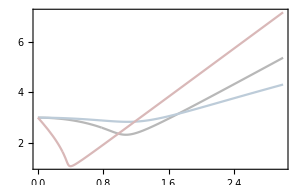

```mathematica
outLRℯ𝒻𝒻=Plot[{BoutLRefftop[ℓ],BoutLReffbottom[ℓ],HoutLRefftop[ℓ],HoutLReffbottom[ℓ],CoutLRefftop[ℓ],CoutLReffbottom[ℓ]},{ℓ,0,3},PlotStyle->{Darker[LightGray,0.15],Darker[LightGray,0.15],Darker[LightBlue,0.15],Darker[LightBlue,0.15],Darker[LightRed,0.15],Darker[LightRed,0.15]},PlotRange->{{0,3},Automatic},Frame->True,ImageSize->300]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::munfl: (1.95068×10^-6)^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.95068×10^-6)^70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.95068×10^-6)^72 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

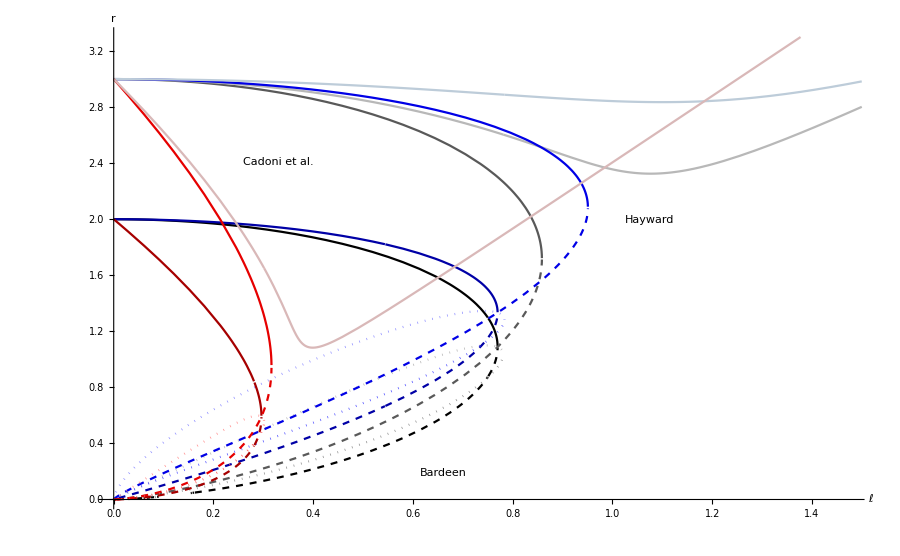

```mathematica
Plot[{SubPlus[rB][1,ℓ],SubMinus[rB][1,ℓ],BoutLRbkg[1,ℓ],BinLRbkg[1,ℓ],BoutLRefftop[ℓ],BoutLReffbottom[ℓ],BinLRefftop[ℓ],BinLReffbottom[ℓ],SubPlus[rH][1,ℓ],SubMinus[rH][1,ℓ],HoutLRbkg[1,ℓ],HinLRbkg[1,ℓ],HoutLRefftop[ℓ],HoutLReffbottom[ℓ],HinLRefftop[ℓ],HinLReffbottom[ℓ],SubPlus[rC][1,ℓ],SubMinus[rC][1,ℓ],CoutLRbkg[1,ℓ],CinLRbkg[1,ℓ],CoutLRefftop[ℓ],CoutLReffbottom[ℓ],CinLRefftop[ℓ],CinLReffbottom[ℓ]},{ℓ,0,1.5},PlotStyle->{Black,{Black,Dashed},Darker[Gray,0.3],{Darker[Gray,0.3],Dashed},Darker[LightGray,0.15],Darker[LightGray,0.15],{Lighter[Gray,0.40],Dotted},{Lighter[Gray,0.10],Dotted},Darker[Blue,0.35],{Darker[Blue,0.35],Dashed},Darker[Blue,0.10],{Darker[Blue,0.10],Dashed},Darker[LightBlue,0.15],Darker[LightBlue,0.15],{Lighter[Blue,0.55],Dotted},{Lighter[Blue,0.3],Dotted},Darker[Red,0.35],{Darker[Red,0.35],Dashed},Darker[Red,0.10],{Darker[Red,0.10],Dashed},Darker[LightRed,0.15],Darker[LightRed,0.15],{Lighter[Red,0.55],Dotted},{Lighter[Red,0.3],Dotted}},PlotRange->{{0,1.475},{0,3.3}},AxesLabel->{"ℓ","r"},AxesStyle->Arrowheads[{0.00,0.02}],Ticks->{Automatic,Automatic},TicksStyle->Directive[FontSize->19],ImageSize->900,Epilog->{Inset[outLRℯ𝒻𝒻,Scaled[{0.80,0.25}]],Inset[Framed[Style["Bardeen",24,Black],RoundingRadius->2,FrameStyle->Black],Scaled[{0.45,0.075}]],Inset[Black,Scaled[{0.517,0.07}]],Inset[Lighter[Black,0.35],Scaled[{0.527,0.08}]],Inset[Lighter[Black,0.70],Scaled[{0.537,0.09}]],Inset[Framed[Style["Hayward",24,Darker[Blue,0.40]],RoundingRadius->2,FrameStyle->Darker[Blue,0.40]],Scaled[{0.72,0.60}]],Inset[Darker[Blue,0.35],Scaled[{0.793,0.595}]],Inset[Darker[Blue,0.10],Scaled[{0.803,0.605}]],Inset[Darker[LightBlue,0.15],Scaled[{0.813,0.615}]],Inset[Framed[Style["Cadoni et al.",24,Darker[Red,0.40]],RoundingRadius->2,FrameStyle->Darker[Red,0.40]],Scaled[{0.235,0.72}]],Inset[Darker[Red,0.40],Scaled[{0.329,0.72}]],Inset[Darker[Red,0.10],Scaled[{0.339,0.73}]],Inset[Darker[LightRed,0.10],Scaled[{0.349,0.74}]]}]
```